# Quantum Benchmarks

## HHL Matrix Creation

## Preliminaries

## Gates

```mathematica
Clear[Ctrl,Phase]
Ctrl[gate_]:=Ctrl[gate]=ArrayFlatten[{{Id,0},{0,gate}}]
Phase[ϕ_,pauli_]:=Phase[ϕ,pauli]=MatrixExp[-ⅈ ϕ pauli]

{Id,X,Y,Z}=PauliMatrix/@{0,1,2,3};
H={{1,1},{1,-1}}/√2;
CNOT=Ctrl[X];
CZ=Ctrl[Z];
SWAP=ArrayFlatten[{{1,0,0},{0,X,0},{0,0,1}}];
SQSWAP=MatrixPower[SWAP,1/2];
NOTC=SWAP.CNOT.SWAP;
MyEcho[x_]:=Module[{},Print[x//MatrixForm];x]
```

```mathematica
MatrixForm/@{Id,X,Y,Z,H,CNOT,CZ,SWAP,SQSWAP,NOTC,Phase[Z,π/2],Phase[Y,π/16]}
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1),(1/(√2) | 1/(√2)
1/(√2) | -1/(√2)),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 1/2-ⅈ/2 | 0
0 | 1/2-ⅈ/2 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0),(-ⅈ | 0
0 | ⅈ),(Cos[π/16] | -Sin[π/16]
Sin[π/16] | Cos[π/16])}

## Matrix Circuits

## VQE Ansatz for U

We seek an ansatz which is interleaved single-qubit and entangling layers; much like a VQE circuit. This is an arbitrary choice of course.

```mathematica
Clear[VQEAnsatz]
VQEAnsatz[width_Integer/;width≥2,blockSize_Integer/;blockSize≥2,depth_Integer/;depth≥1,singleQubitGateCount_Integer/;singleQubitGateCount≥1]:=Flatten@Join[Table[{
SingleQubitLayer@@RandomChoice[Range@singleQubitGateCount,width],
EntanglingLayer@@If[EvenQ@width,
If[EvenQ@i,
{{1}}~Join~Partition[Range[2,width-1],2]~Join~{{width}},
Reverse/@Reverse@Partition[Reverse@Range[width],2]
],
If[EvenQ@i,
Partition[Range[width],UpTo[2]],
Reverse/@Reverse@Partition[Reverse@Range[width],UpTo[2]]
]
]
},
{i,1,depth}
],{SingleQubitLayer@@RandomChoice[Range@singleQubitGateCount,width]}
]

Clear[UnitaryMatrixListQ,GateSetQ,RandomVQESample]
UnitaryMatrixListQ[list_]:=ListQ[list]∧(Length@list>0)∧And@@(UnitaryMatrixQ/@list)∧Equal@@(Dimensions/@list)∧(Dimensions@First@list=={2,2})
GateSetQ[assoc_]:=AssociationQ[assoc]∧UnitaryMatrixListQ@Values[assoc]
Clear[kron]
kron[mat_?MatrixQ]:=mat
kron[other__]:=KroneckerProduct[other]
RandomVQESample[width_Integer/;width≥2,blockSize_Integer/;blockSize≥2,depth_Integer/;depth≥1,entanglingGate_?UnitaryMatrixQ,entanglingGateName_String,singleQubitGates_?GateSetQ,numeric_:True]:=
Module[{
singleQubitGatesN=Values@singleQubitGates//If[numeric,N,Identity],
entanglingGateN=entanglingGate//If[numeric,N,Identity],
ansatz,U,textual
},
ansatz=VQEAnsatz[width,blockSize,depth,Length@singleQubitGates];
U=Dot@@(ansatz//.{
SingleQubitLayer[l___,gateIdx_Integer,r___]:>SingleQubitLayer[l,singleQubitGatesN⟦gateIdx⟧,r],
EntanglingLayer[l___,gateIdcs_?VectorQ,r___]:>EntanglingLayer[l,If[Length@gateIdcs==1,Id,entanglingGateN],r]
}/.{
SingleQubitLayer->kron,
EntanglingLayer->kron
}
);
textual=ansatz//.{
SingleQubitLayer[gateIdcs__]:>MapIndexed[Function[{idx,lane},Keys[singleQubitGates]⟦idx⟧<>" "<>ToString[lane⟦1⟧]],{gateIdcs}],
EntanglingLayer[gateIdcs__]:>(If[Length@#==1,Nothing,entanglingGateName<>" "<>StringRiffle[ToString/@#, " "]]&/@{gateIdcs})
}//Flatten;

<|
"ansatz"->ansatz,
"textual"->(textual//Reverse),
"U"->U//Chop,
"B"->U[[-blockSize;;,-blockSize;;]]//Chop,
(*"Histogram"->(Table[(Abs[#^2]&)/@((U[[1;;blockSize,1;;blockSize]]//Inverse).IdentityMatrix[blockSize][[k]]),{k,1,blockSize}]//Transpose),*)
"Histogram"->(Table[(Abs[#^2]&)/@((U[[-blockSize;;,-blockSize;;]]//PseudoInverse).IdentityMatrix[blockSize][[k]]),{k,1,blockSize}]//Transpose),
"qubits"->Log[2,Length[U]]
|>
]
```

```mathematica
VQEAnsatz[4,2,2,5]
```

{SingleQubitLayer[4,1,3,1],EntanglingLayer[{1,2},{3,4}],SingleQubitLayer[4,5,4,4],EntanglingLayer[{1},{2,3},{4}],SingleQubitLayer[2,2,5,4]}

The RandomVQESample function expects a circuit width (i.e. how many qubits U should act on), an ansatz depth, an entangling gate plus name, and a single qubit gate list defined in the following. This can of course be changed to include other rotations.

```mathematica
gateset=<|
"I"->IdentityMatrix[2],
"X"->X,
"Y"->Y,
"Z"->Z,
"R"->Phase[Z,π/3],
"S"->Phase[Z,π/4],
"T"->Phase[Z,π/8],
"RX"->Phase[X,π/3],
"SX"->Phase[X,π/4],
"TX"->Phase[X,π/8],
"RY"->Phase[Y,π/3],
"SY"->Phase[Y,π/4],
"TY"->Phase[Y,π/8]
|>;
MatrixForm/@%
```

<|I→(1 | 0
0 | 1),X→(0 | 1
1 | 0),Y→(0 | -ⅈ
ⅈ | 0),Z→(1 | 0
0 | -1),R→(ⅇ^(-(ⅈ π)/3) | 0
0 | ⅇ^((ⅈ π)/3)),S→(ⅇ^(-(ⅈ π)/4) | 0
0 | ⅇ^((ⅈ π)/4)),T→(ⅇ^(-(ⅈ π)/8) | 0
0 | ⅇ^((ⅈ π)/8)),RX→(1/2 (-1)^(1/3)-1/2 (-1)^(2/3) | -1/2 (-1)^(1/3)-1/2 (-1)^(2/3)
-1/2 (-1)^(1/3)-1/2 (-1)^(2/3) | 1/2 (-1)^(1/3)-1/2 (-1)^(2/3)),SX→(1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2)),TX→(1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | -1/2 (-1)^(1/8)-1/2 (-1)^(7/8)
-1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | 1/2 (-1)^(1/8)-1/2 (-1)^(7/8)),RY→(1/2 | -(√3)/2
(√3)/2 | 1/2),SY→(1/(√2) | -1/(√2)
1/(√2) | 1/(√2)),TY→(Cos[π/8] | -Sin[π/8]
Sin[π/8] | Cos[π/8])|>

```mathematica
RandomVQESample[2,2,3,CZ,"CZ",gateset]
```

<|ansatz→{SingleQubitLayer[9,2],EntanglingLayer[{1,2}],SingleQubitLayer[6,10],EntanglingLayer[{1},{2}],SingleQubitLayer[1,12],EntanglingLayer[{1,2}],SingleQubitLayer[11,7]},textual→{T 2,RY 1,CZ 1 2,SY 2,I 1,TX 2,S 1,CZ 1 2,X 2,SX 1},U→{{0.+0.183013 ⅈ,0.683013,0.+0.683013 ⅈ,-0.183013},{0.-0.683013 ⅈ,0.183013,0.+0.183013 ⅈ,0.683013},{-0.683013,0.+0.183013 ⅈ,0.183013,0.+0.683013 ⅈ},{0.183013,0.+0.683013 ⅈ,0.683013,0.-0.183013 ⅈ}},B→{{0.183013,0.+0.683013 ⅈ},{0.683013,0.-0.183013 ⅈ}},Histogram→{{0.133975,1.86603},{1.86603,0.133975}},qubits→2|>

## Find Good Circuit Candidates

```mathematica
(* checks that the top bs x bs block has bs^2-minOffset many unique absolute value squared entries *)
Clear[CircuitCriterion]
CircuitCriterion[bs_Integer,threshold_:.01,minOffset_:1,distinctSVs_:2,conditonNum_:2,minProb_:0.2]:=Function[U,
(
Length@Union@Rationalize[#,threshold]&@Abs@N@Flatten@U⟦-bs;;,-bs;;⟧≥bs^2-minOffset
)∧(
(* condition number criterion *)
Max[SingularValueList[U⟦-bs;;,-bs;;⟧]]/ Min[SingularValueList[U⟦-bs;;,-bs;;⟧]//DeleteCases[#==0&]]<=conditonNum
)∧(
(* distinct singular values criterion *)
(SingularValueList[U⟦-bs;;,-bs;;⟧]//DeleteDuplicatesBy[#,Round[500*#]&]&//Length)≥distinctSVs
)∧(
(* enforce large probability entries in every column *)
(Apply[Max,Transpose[Abs[#]^2&/@PseudoInverse[U⟦-bs;;,-bs;;⟧]]*(Min[SingularValueList[U⟦-bs;;,-bs;;⟧]//DeleteCases[#==0&]])^2,1]//Min)>minProb
)
]
```

```mathematica
CircuitCriterion[5][RandomReal[{1,5},{10,10}]]&/@Range[10]
CircuitCriterion[5][IdentityMatrix[10]]
```

{True,True,True,True,True,True,True,False,True,True}

False

```mathematica
Clear[MatPlot]
MatPlot[U_?UnitaryMatrixQ,bs_Integer]:=BarChart3D[MyEcho[Abs[#]^2&/@U⟦-bs;;,-bs;;⟧],ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"FaceGrids"->None,"Canvas"->False]⟦1⟧//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

Re-run the following or increase trials if it doesn’t print out a final matrix.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

176+Match found after + trials

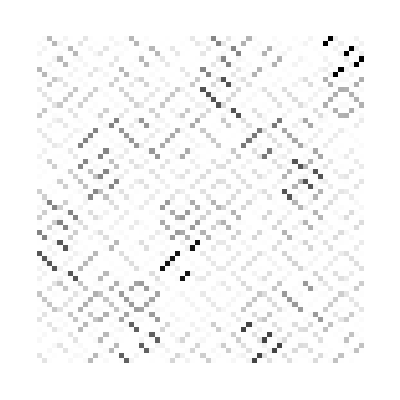

64

{0.822664,0.568527}

{SX 7,SY 6,SY 5,Z 4,Z 3,RY 2,Y 1,CX 5 6,CX 3 4,CX 1 2,Y 7,Y 6,SY 5,Z 4,R 3,T 2,SY 1,CX 6 7,CX 4 5,CX 2 3,RX 7,SX 6,S 5,RX 4,Z 3,R 2,R 1,CX 5 6,CX 3 4,CX 1 2,TX 7,S 6,R 5,TY 4,I 3,Z 2,TY 1,CX 6 7,CX 4 5,CX 2 3,RX 7,RX 6,TX 5,TY 4,I 3,X 2,SX 1,CX 5 6,CX 3 4,CX 1 2,SX 7,I 6,T 5,SY 4,S 3,T 2,SY 1,CX 6 7,CX 4 5,CX 2 3,R 7,I 6,R 5,Z 4,TY 3,TY 2,R 1}

```mathematica
theVQE=Module[{
theVQE,
lowerRightBlockSize=64(* dimension *)
},

Module[{
width=7,  (* number of overall qubits *)
depth=6,  (* ansatz depth *)
entanglingGate=CNOT,
entanglingGateName="CX",
singleQubitGates=gateset,
i,maxTrials=10000,
criterionF=CircuitCriterion[lowerRightBlockSize,.007,2^20-100,2,2,0.1] (* play with the two threshold parameters in case you don't get a hit *)
},
For[i=1,i≤maxTrials,i++;
With[{
vqe=RandomVQESample[width,lowerRightBlockSize,depth,entanglingGate,entanglingGateName,singleQubitGates,True]
},
If[criterionF@vqe["U"],
theVQE=vqe;
Print["Match found after "+i+" trials"];
Break[];
]
]
]
];


(*MatPlot[theVQE["U"],lowerRightBlockSize]//Print;*)
theVQE
];

(Abs[#]^2&/@PseudoInverse[theVQE["B"]])//ArrayPlot
(*theVQE["B"]//MatrixForm*)
theVQE["B"]//SingularValueList;
%//Length
DeleteDuplicatesBy[%%,Round[500*#]&]
theVQE["textual"]
```

## Polynomial Coefficients

```mathematica
(*Finds the largest absolute value on the interval[-1,1]*)
findPolyMaxAbs[poly_]:=Module[{deriv=D[poly,x],roots,optimaCandidates},roots=If[TrueQ@Element[deriv,Complexes],{},x/.NSolve[deriv==0,x]];
optimaCandidates=Join[{-1},roots,{1}];
(poly/.x->optimaCandidates)//Abs//Max];
(*Lowest degree problem specific polynomial*)
fitOddPoly[singularValues_]:=fitOptimizedPoly[singularValues,0,1];
(*Optimise the magnitude of the polynomial on[-1,1]*)
fitOptimizedPoly[singularValues_,numExtraPoints_,numRandomTrials_]:=Module[{distinctSVs=DeleteDuplicates[singularValues],fitPoints,tmpPoly,currentMinMax=Infinity,currentBestPoly},
For[j=0,j<numRandomTrials,j++,fitPoints=Join[distinctSVs,Table[RandomReal[{0,2}],{k,1,numExtraPoints}]];
fitPoints=DeleteCases[Join[fitPoints,-fitPoints]//N,0.0];
tmpPoly=InterpolatingPolynomial[{#,1/#}&/@fitPoints,x];
tmpPoly=((tmpPoly-(tmpPoly/.x->-x))/2)//Simplify;
currentBestPoly=If[findPolyMaxAbs[tmpPoly]<currentMinMax,tmpPoly,currentBestPoly];
currentMinMax=If[findPolyMaxAbs[tmpPoly]<currentMinMax,findPolyMaxAbs[tmpPoly],currentMinMax];];
currentBestPoly];
```

8.16340150682514398283728951355 x-93.535233688532741780363721773 x^3+301.218044752806861197313992307 x^5-363.174288416582953686884138733 x^7+147.48251920406232784444000572 x^9

{0.995078,0.936608,0.35037810813806799,0.0990974}

0.+112.125 x-1067.05 x^3+1909.86 x^5-954.93 x^7

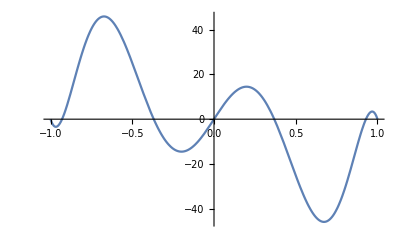

45.835

0.+114.27 x-1307.51 x^3+4198.18 x^5-5050.67 x^7+2047.87 x^9

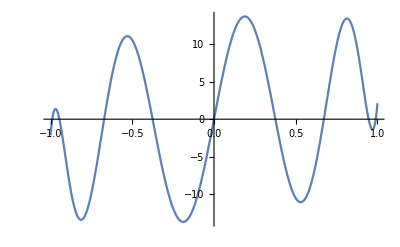

13.7394

```mathematica
(*Some tests and demos for the above*)
poly=8.1634015068251439828372895135544240474700927734375`30. x-93.53523368853274178036372177302837371826171875`30. x^3+301.21804475280686119731399230659008026123046875`30. x^5-363.1742884165829536868841387331485748291015625`30. x^7+147.482519204062327844440005719661712646484375`30. x^9
singularValues={0.99507773624,0.936608339348,0.350378108138067994,0.09909742093286229}
%//fitOddPoly
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
optPoly1=fitOptimizedPoly[%%%%,1,100]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
(*fitOptimizedPoly[%%%%%%%,2,10000]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs*)
```

```mathematica
(*Computes the pair of polynomials that correspond to the given real part, see more in https://arxiv.org/abs/1806.01838 *)
getPolyPairs[poly_,precision_]:=Module[{polyTry,K,roots,Qp,Zp,SRp,LRp,Ip,Wp,genRoots,zeroRoots,smallRealRoots,largeRealRoots,imgRoots,parityTrick,Bp,Cp},
polyTry=SetPrecision[poly,precision];
degree = (CoefficientList[polyTry,x]//Length)-1;
(K=Sqrt[-Coefficient[(1-polyTry^2//Expand),x^(2 degree)]])//Precision;
roots=x/.NSolve[(1-polyTry^2//Expand)==0,x,WorkingPrecision->precision];
(*p=ListPlot[{Re[#],Im[#]}&/@%,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];
Show[p,Graphics@Circle[{0,0},1]]*)
(genRoots=Select[roots,(Re[#]>0&& Im[#]>0)&]);
zeroRoots=(Select[roots,(#==0)&]);
smallRealRoots=(Select[roots,(#!=0&&Re[#]>-1&&Re[#]<1&& Im[#]==0)&]);
(smallRealRoots=Table[smallRealRoots[[4i-3]],{i,1,(smallRealRoots//Length)/4}]);
(largeRealRoots=Select[roots,(Re[#]≥1&& Im[#]==0)&]);
(imgRoots=Select[roots,(Re[#]==0&& Im[#]>0)&]);
Qp=(#[[2]]x^2-#[[1]]+I Sqrt[#[[2]]^2-1]x Sqrt[1-x^2])&/@({Abs[#]^2,Abs[#]^2+Sqrt[2(Re[#]^2+1)Im[#]^2+(Re[#]^2-1)^2+Im[#]^4]}&/@genRoots) ;
Zp=x^((zeroRoots//Length)/2);
SRp=(x^2-#^2)&/@smallRealRoots;
LRp=(Sqrt[#^2-1]x+I # Sqrt[1-x^2])&/@largeRealRoots;
Ip=(Sqrt[Abs[#]^2+1]x-I Abs[#]Sqrt[1-x^2])&/@imgRoots;
Wp=K*(Times@@Qp)*Zp*(Times@@SRp)*(Times@@LRp)*(Times@@Ip)//Expand//Simplify;
parityTrick=SetPrecision[Wp/.{Sqrt[1-x^2]->-I},precision];
Bp=SetPrecision[(parityTrick+(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
Cp=SetPrecision[(parityTrick-(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
{Bp,Cp}
]
```

True

8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9

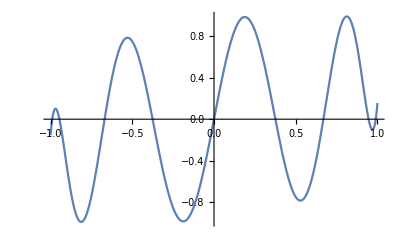

True

```mathematica
(*Some tests and demos for the above*)
{Bp,Cp}=getPolyPairs[ChebyshevT[5,x] ,110];
Bp^2+(1-x^2)Cp^2+ChebyshevT[5,x]^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
poly=8.163401506825144 x-93.53523368853274 x^3+301.21804475280686 x^5-363.17428841658295 x^7+147.48251920406233 x^9
Plot[%,{x,-1,1}]
{Bp,Cp}=getPolyPairs[poly,30];
poly=SetPrecision[poly,30];
Bp^2+(1-x^2)Cp^2+poly^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
```

```mathematica
(*Computes the sequence of angles for a given polynomial, see more in https://arxiv.org/abs/1806.01838 *)
getAngles[poly_,precision_Integer:10]:=Module[{tmpPoly,agreement,tmpprecision,Bp,Cp,Mat,carved,phs,phaseGates,W,NewMat},
agreement=1;
tmpprecision=MachinePrecision;
phs={};
While[ ((agreement//Accuracy) <precision) ||(agreement>10^-precision),
tmpPoly=SetPrecision[poly,tmpprecision];
{Bp,Cp}=getPolyPairs[tmpPoly,tmpprecision];
(Mat={{tmpPoly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,tmpPoly-I Bp}})//MatrixForm;
carved=NestList[carveLastAngle[#[[1]]]&,{Mat,{}},(tmpPoly//CoefficientList[#,x]&//Length)-1];
phs=Join[{(carved//Last)[[1]][[1]][[1]]},(#[[2]]&/@ carved)//Reverse//Most];
NewMat=getWMatrix[phs];
agreement=(NewMat[[1,1]]-tmpPoly-I Bp)//Expand//CoefficientList[#,x]&//Abs//Total;
Print[tmpprecision];
tmpprecision=2tmpprecision];
phs//Arg
];
carveLastAngle[Mat_]:=Module[{phase,outMat},
phase=(Coefficient[Mat[[1,1]],x,Exponent[Mat[[1,1]],x]]/(Coefficient[Mat[[1,2]]/.{Sqrt[1-x^2]->-I},x,(Exponent[Mat[[1,1]],x]-1)]))//Sqrt;
outMat=Mat.{{Conjugate[phase],0},{0,phase}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand;
outMat=outMat/.x^b_/;b≥Exponent[Mat[[1,1]],x]+1->0;
outMat=outMat/.Sqrt[1-x^2]x^b_/;b≥Exponent[Mat[[1,1]],x]->0;
{outMat, phase}
];
getWMatrix[phs_]:=Module[{phaseGates,W},
phaseGates=Table[{{phs[[i]],0},{0,Conjugate[phs[[i]]]}},{i,1,Length[phs]}];
(W={{x,I Sqrt[1-x^2]},{I Sqrt[1-x^2],x}})//MatrixForm;
(Dot@@((phaseGates//Most).W)).(phaseGates//Last)//Expand
];
WAnglesToRAngles[angles_]:=Module[{tmpAngles=angles},
tmpAngles[[1]]+=Last[angles]+((Mod[(Length[angles]),4])-1)Pi/2;
Mod[#,2 Pi]&/@Drop[tmpAngles,-1]-Pi/2];
getRMatrix[angles_]:=Module[{phaseGates,R},
phaseGates=Table[{{Exp[I angles[[i]]],0},{0,Exp[-I angles[[i]]]}},{i,1,Length[angles]}];
(R={{x, Sqrt[1-x^2]},{ Sqrt[1-x^2],-x}})//MatrixForm;
(Dot@@(phaseGates.R))//Expand
];
```

```mathematica
(*Some tests and demos for the above*)
angles=getAngles[ChebyshevT[10,x],20]//Chop
(getWMatrix[Exp[I%]])[[1,1]]-ChebyshevT[10,x]//Chop
(getRMatrix[%%//WAnglesToRAngles])[[1,1]]-ChebyshevT[10,x]//Expand//Chop
tmpPoly=poly/findPolyMaxAbs[poly]//Expand
angles=getAngles[%,20]
((getWMatrix[Exp[I%]//Reverse])[[1,1]]-%%)//CoefficientList[#,x]&//Re//Abs//Total//Chop
((getRMatrix[%%//WAnglesToRAngles])[[1,1]]-%%%)//CoefficientList[#,x]&//Re//Abs//Total//Chop
(*This is what we need to feed to the QSVT circuit*)
%%%//WAnglesToRAngles//Reverse//SetPrecision[#,MachinePrecision]&
```

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{-0.785398163397448309615660845819875721049292349843776,0,0,0,0,0,0,0,0,0,0.785398163397448309615660845819875721049292349843776455243736148}

0

0

8.27720505405564551123137 x-94.8391805023565269774823 x^3+305.417235733924878686473 x^5-368.237192923995131082338 x^7+149.538529045778466957024 x^9

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{-0.408901635471894571772110507561051468532631544752781,0.3584552943894671048461378497305384989146988780925645,0.13603714837731554333554206592563397208622491414361709,0.0886809496145304613134064710023385996384743201663036807,-0.2528935548135681432431437582642864394177341833368914951,-0.252893554813568143243143758264286439417734183336891495115,0.08868094961453046131340647100233859963847432016630368068608,0.13603714837731554333554206592563397208622491414361708991167,0.358455294389467104846137849730538498914698878092564541323801,1.16189469132300204745921118407869997356595315493477190490618146}

0

0

{-1.21234,-1.43476,-1.48212,4.4595,4.4595,-1.48212,-1.43476,-1.21234,0.752993}

```mathematica
Clear[anglesForCircuit];
anglesForCircuit[vqe_Association,verbose_Symbol:False]:=Module[{
U=vqe["U"],
blockEncoding,
SVs,
interPolys, interPolysMaxAbs,
objectiveFunction, optimumDeg,
interPoly,
subnormalisation,
print=If[verbose,Print,Identity]
},
blockEncoding=U[[-Length[U]/2;;,-Length[U]/2;;]];
blockEncoding//MatrixForm//print;
If[verbose&&False,MatPlot[U,Length[blockEncoding]]//print,False];
blockEncoding//Inverse//MatrixForm//print;
If[verbose&&False,MatInvPlot[blockEncoding]//print,False];
blockEncoding.Inverse[blockEncoding]//MatrixForm//Chop//print;
SVs=SingularValueList[blockEncoding];
SVs=DeleteDuplicatesBy[SVs,Round[500*#]&];
print[SVs];
print[DeleteDuplicates[SVs]];
interPolys=Table[fitOptimizedPoly[SVs,i,100^i],{i,0,1}];
interPolysMaxAbs=findPolyMaxAbs/@interPolys;
For[i=1,i≤Length[interPolys],i++,Plot[interPolys[[i]],{ x,-1,1}]//print];
objectiveFunction=1/interPolysMaxAbs/(Length[CoefficientList[#,x]]&/@interPolys);
optimumDeg=(Position[objectiveFunction,Max[objectiveFunction]]//Flatten)[[1]];
print[optimumDeg];
interPoly=interPolys[[optimumDeg]];
subnormalisation=0.9999/findPolyMaxAbs[interPoly];
interPoly=subnormalisation*interPoly//Expand;
print[interPoly];
{subnormalisation,getAngles[interPoly,8]//WAnglesToRAngles//Reverse//SetPrecision[#,MachinePrecision]&}
];
Clear[MatInvPlot];
MatInvPlot[mat_]:=
BarChart3D[MyEcho[(Abs[#])^2&/@Inverse[mat]]//Transpose,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"FaceGrids"->None,"Canvas"->False]⟦1⟧//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&;
```

```mathematica
anglesForCircuit[theVQE,True]
```

anglesForCircuit[theVQE$2500,True]

## Export Candidates to Python

```mathematica
exportCandidate[vqe_Association]:=Module[{str="",idleRemoved=vqe["textual"]//DeleteCases[#,x_/;StringTake[x,2]=="I "]&,angles,subnorm},
{subnorm,angles}=anglesForCircuit[vqe];
Print[subnorm];
str=str<>"{\n    \"qubits\": ";
str=str<>(vqe["qubits"]//ToString)<>",";
str=str<>"\n    \"ancillas\": 1,";
str=str<>"\n    \"circuit\": [";
str=str<>StringRiffle["("<>StringReplace["\""<>StringReplace[#," "->"\" ",1]," "->", "]<>")"&/@(idleRemoved),", "]<>"],\n";
str=str<>"    \"angles\": [";
str=str<>StringRiffle[ToString/@angles,", "]<>"],\n";
str=str<>"    \"histogram\": [\t";
str=str<>StringRiffle[("["<>StringRiffle[(ToString[#,CForm])&/@#,", "]<>"]")&/@(subnorm^2*vqe["Histogram"]),",\n\t\t\t\t\t"]<>"],\n";
str=str<>"}";
str
]
```

```mathematica
exportCandidate[theVQE]
```

MachinePrecision

0.568272

{
    "qubits": 7,
    "ancillas": 1,
    "circuit": [("SX", 7), ("SY", 6), ("SY", 5), ("Z", 4), ("Z", 3), ("RY", 2), ("Y", 1), ("CX", 5, 6), ("CX", 3, 4), ("CX", 1, 2), ("Y", 7), ("Y", 6), ("SY", 5), ("Z", 4), ("R", 3), ("T", 2), ("SY", 1), ("CX", 6, 7), ("CX", 4, 5), ("CX", 2, 3), ("RX", 7), ("SX", 6), ("S", 5), ("RX", 4), ("Z", 3), ("R", 2), ("R", 1), ("CX", 5, 6), ("CX", 3, 4), ("CX", 1, 2), ("TX", 7), ("S", 6), ("R", 5), ("TY", 4), ("Z", 2), ("TY", 1), ("CX", 6, 7), ("CX", 4, 5), ("CX", 2, 3), ("RX", 7), ("RX", 6), ("TX", 5), ("TY", 4), ("X", 2), ("SX", 1), ("CX", 5, 6), ("CX", 3, 4), ("CX", 1, 2), ("SX", 7), ("T", 5), ("SY", 4), ("S", 3), ("T", 2), ("SY", 1), ("CX", 6, 7), ("CX", 4, 5), ("CX", 2, 3), ("R", 7), ("R", 5), ("Z", 4), ("TY", 3), ("TY", 2), ("R", 1)],
    "angles": [4.19379, 4.19379, -0.533589],
    "histogram": [	[0.00008173544887050613, 0.004715765999816757, 0.06568214723187125, 0.001138427942986238, 0.00019747777274617146, 0.01139357499475275, 0.0008180218802369861, 0.000014178266175561464, 0.00041309586709186526, 0.023833764561357905, 0.001711187305879553, 0.000029658948843730965, 0.000011430786268473778, 0.0006595047067208551, 0.009185715586531295, 0.00015921031422914703, 0.00008351466587205952, 0.004818418779708043, 0.06711191601234964, 0.001163209238974614, 0.00005740814279756772, 0.003312190385670978, 0.00023780457040369134, 4.121719208748305e-6, 0.00002379680630768935, 0.0013729681752628505, 0.00009857467991839807, 1.7085338226512278e-6, 0.000027731137801858285, 0.001599961321426435, 0.02228458644540773, 0.000386244923111079, 0.00013955709192746597, 0.008051813481657335, 0.11214729454479554, 0.0019437795385920506, 0.00039835070459395274, 0.022983035325386314, 0.001650107694826588, 0.000028600293807321195, 0.001222200851795193, 0.07051546546191867, 0.005062782635784655, 0.00008775007311341335, 5.495023328055285e-6, 0.0003170380114960684, 0.004415769855839662, 0.00007653580166826371, 4.042171295380536e-6, 0.00023321501531592306, 0.0032482661296720406, 0.00005630018329364496, 0.00017833797309984176, 0.010289295056700015, 0.0007387381478132314, 0.000012804090387781501, 0.004109278092104474, 0.2370867742004912, 0.017022064531995052, 0.00029503289291272486, 0.000015047422181022042, 0.0008681682536371447, 0.012092023874731373, 0.00020958355422904723],
					[0.004715765999816769, 0.00008173544887050949, 0.0011384279429862332, 0.06568214723187128, 0.011393574994752752, 0.00019747777274616422, 0.000014178266175563187, 0.0008180218802369856, 0.023833764561357964, 0.00041309586709185485, 0.000029658948843735505, 0.0017111873058795483, 0.0006595047067208597, 0.000011430786268474873, 0.00015921031422915107, 0.009185715586531303, 0.00481841877970805, 0.00008351466587206123, 0.0011632092389746369, 0.06711191601234955, 0.003312190385671001, 0.000057408142797568315, 4.121719208748382e-6, 0.00023780457040368838, 0.0013729681752628526, 0.0000237968063076912, 1.7085338226511133e-6, 0.00009857467991840174, 0.0015999613214264575, 0.000027731137801859258, 0.0003862449231110833, 0.022284586445407754, 0.00805181348165736, 0.00013955709192747023, 0.0019437795385920688, 0.11214729454479544, 0.02298303532538634, 0.00039835070459395106, 0.000028600293807320226, 0.0016501076948265995, 0.07051546546191871, 0.0012222008517951699, 0.00008775007311341328, 0.005062782635784706, 0.0003170380114960693, 5.495023328055621e-6, 0.00007653580166826285, 0.0044157698558396664, 0.00023321501531592788, 4.04217129537997e-6, 0.00005630018329364245, 0.003248266129672049, 0.0102892950567, 0.00017833797309984437, 0.00001280409038778133, 0.0007387381478132329, 0.23708677420049126, 0.0041092780921044335, 0.00029503289291272437, 0.017022064531995052, 0.0008681682536371329, 0.000015047422181023297, 0.00020958355422903967, 0.012092023874731399],
					[0.0001974777727461655, 0.011393574994752765, 0.0008180218802369784, 0.000014178266175562466, 0.00008173544887050679, 0.0047157659998167765, 0.06568214723187125, 0.0011384279429862494, 0.000011430786268475091, 0.0006595047067208688, 0.009185715586531336, 0.00015921031422915527, 0.0004130958670918531, 0.023833764561357936, 0.0017111873058795496, 0.000029658948843733872, 0.00005740814279756924, 0.0033121903856709912, 0.00023780457040369307, 4.121719208747723e-6, 0.0000835146658720599, 0.004818418779708017, 0.06711191601234962, 0.0011632092389746173, 0.00002773113780185941, 0.0015999613214264556, 0.022284586445407758, 0.00038624492311107884, 0.000023796806307689274, 0.0013729681752628446, 0.0000985746799183961, 1.7085338226514496e-6, 0.0003983507045939489, 0.022983035325386317, 0.0016501076948265995, 0.00002860029380732017, 0.00013955709192746792, 0.0080518134816573, 0.1121472945447955, 0.0019437795385920734, 5.495023328056083e-6, 0.00031703801149606984, 0.004415769855839689, 0.0000765358016682628, 0.0012222008517951846, 0.0705154654619188, 0.005062782635784678, 0.00008775007311341526, 0.00017833797309984027, 0.010289295056700024, 0.0007387381478132286, 0.000012804090387782662, 4.042171295380653e-6, 0.00023321501531593314, 0.0032482661296720744, 0.00005630018329364544, 0.000015047422181022982, 0.0008681682536371297, 0.012092023874731373, 0.0002095835542290487, 0.004109278092104438, 0.23708677420049143, 0.017022064531995035, 0.0002950328929127243],
					[0.0113935749947528, 0.00019747777274616742, 0.000014178266175562645, 0.0008180218802369807, 0.0047157659998167635, 0.00008173544887050805, 0.001138427942986228, 0.06568214723187125, 0.0006595047067208536, 0.000011430786268473671, 0.0001592103142291498, 0.009185715586531336, 0.023833764561358002, 0.00041309586709185555, 0.00002965894884373442, 0.0017111873058795503, 0.0033121903856709926, 0.0000574081427975679, 4.121719208748801e-6, 0.00023780457040368982, 0.004818418779708026, 0.00008351466587206282, 0.0011632092389746206, 0.06711191601234968, 0.0015999613214264469, 0.000027731137801861182, 0.00038624492311107694, 0.02228458644540772, 0.001372968175262858, 0.000023796806307688423, 1.7085338226514544e-6, 0.00009857467991840442, 0.02298303532538638, 0.00039835070459394954, 0.00002860029380731953, 0.001650107694826591, 0.008051813481657361, 0.00013955709192747326, 0.0019437795385920512, 0.11214729454479559, 0.00031703801149606924, 5.495023328056409e-6, 0.00007653580166826213, 0.004415769855839656, 0.07051546546191892, 0.0012222008517951853, 0.00008775007311341352, 0.005062782635784689, 0.010289295056699984, 0.0001783379730998409, 0.000012804090387781613, 0.0007387381478132247, 0.00023321501531593103, 4.0421712953803845e-6, 0.00005630018329364409, 0.0032482661296720765, 0.0008681682536371275, 0.00001504742218102278, 0.0002095835542290434, 0.012092023874731421, 0.23708677420049173, 0.0041092780921044925, 0.00029503289291271363, 0.017022064531994948],
					[0.0008180218802369837, 0.000014178266175561564, 0.00019747777274617238, 0.011393574994752692, 0.06568214723187124, 0.001138427942986241, 0.00008173544887050914, 0.004715765999816757, 0.009185715586531295, 0.0001592103142291529, 0.000011430786268475438, 0.0006595047067208395, 0.00171118730587956, 0.000029658948843733062, 0.00041309586709186515, 0.02383376456135801, 0.00023780457040369207, 4.121719208747583e-6, 0.000057408142797571764, 0.0033121903856709522, 0.06711191601234974, 0.0011632092389746089, 0.00008351466587205893, 0.004818418779708006, 0.02228458644540777, 0.00038624492311107374, 0.000027731137801859437, 0.001599961321426421, 0.00009857467991839831, 1.7085338226520709e-6, 0.000023796806307692093, 0.001372968175262846, 0.0016501076948265978, 0.000028600293807319647, 0.0003983507045939485, 0.02298303532538621, 0.11214729454479569, 0.001943779538592057, 0.00013955709192746535, 0.008051813481657325, 0.004415769855839674, 0.00007653580166826102, 5.495023328054765e-6, 0.000317038011496061, 0.005062782635784706, 0.00008775007311341096, 0.0012222008517951608, 0.07051546546191877, 0.0007387381478132335, 0.000012804090387779917, 0.0001783379730998459, 0.010289295056699985, 0.003248266129672084, 0.00005630018329364208, 4.042171295379057e-6, 0.00023321501531592832, 0.012092023874731395, 0.00020958355422903574, 0.000015047422181021731, 0.000868168253637146, 0.017022064531995063, 0.0002950328929127189, 0.004109278092104459, 0.23708677420049112],
					[0.000014178266175561732, 0.0008180218802369916, 0.011393574994752804, 0.00019747777274616943, 0.0011384279429862418, 0.06568214723187125, 0.004715765999816759, 0.00008173544887050857, 0.00015921031422914768, 0.00918571558653133, 0.0006595047067208506, 0.000011430786268474066, 0.00002965894884373382, 0.0017111873058795546, 0.023833764561358047, 0.000413095867091865, 4.1217192087471585e-6, 0.0002378045704036936, 0.0033121903856710086, 0.00005740814279756349, 0.0011632092389746323, 0.06711191601234966, 0.004818418779708041, 0.00008351466587206228, 0.0003862449231110747, 0.022284586445407723, 0.0015999613214264458, 0.000027731137801859634, 1.7085338226515349e-6, 0.00009857467991839988, 0.001372968175262861, 0.000023796806307691483, 0.00002860029380731932, 0.0016501076948266017, 0.022983035325386317, 0.0003983507045939486, 0.001943779538592082, 0.11214729454479547, 0.008051813481657327, 0.0001395570919274714, 0.00007653580166826182, 0.004415769855839663, 0.00031703801149607054, 5.495023328055011e-6, 0.00008775007311341303, 0.00506278263578467, 0.07051546546191874, 0.0012222008517951718, 0.000012804090387783338, 0.0007387381478132388, 0.010289295056700043, 0.0001783379730998408, 0.000056300183293647146, 0.003248266129672057, 0.00023321501531592596, 4.0421712953801685e-6, 0.00020958355422904867, 0.012092023874731472, 0.0008681682536371333, 0.000015047422181023944, 0.0002950328929127214, 0.017022064531994997, 0.23708677420049143, 0.004109278092104447],
					[0.06568214723187135, 0.0011384279429862336, 0.00008173544887050976, 0.004715765999816742, 0.0008180218802369822, 0.000014178266175562693, 0.00019747777274616582, 0.011393574994752763, 0.0017111873058795767, 0.00002965894884373549, 0.0004130958670918614, 0.023833764561357988, 0.009185715586531378, 0.00015921031422915394, 0.000011430786268474446, 0.0006595047067208661, 0.06711191601234957, 0.0011632092389746275, 0.00008351466587206356, 0.004818418779708038, 0.00023780457040368743, 4.121719208747529e-6, 0.000057408142797569345, 0.003312190385671012, 0.00009857467991840022, 1.708533822651541e-6, 0.000023796806307688945, 0.0013729681752628453, 0.0222845864454077, 0.00038624492311108117, 0.000027731137801858492, 0.0015999613214264443, 0.11214729454479556, 0.0019437795385920486, 0.00013955709192747565, 0.008051813481657316, 0.0016501076948265954, 0.000028600293807320186, 0.00039835070459395605, 0.02298303532538635, 0.005062782635784686, 0.00008775007311341618, 0.0012222008517951773, 0.0705154654619188, 0.004415769855839636, 0.00007653580166826213, 5.49502332805582e-6, 0.0003170380114960688, 0.003248266129672088, 0.00005630018329364299, 4.0421712953801515e-6, 0.00023321501531592767, 0.0007387381478132362, 0.000012804090387781998, 0.0001783379730998437, 0.010289295056699977, 0.01702206453199509, 0.0002950328929127176, 0.0041092780921044535, 0.23708677420049146, 0.012092023874731348, 0.0002095835542290408, 0.00001504742218102398, 0.0008681682536371355],
					[0.0011384279429862447, 0.06568214723187128, 0.004715765999816759, 0.0000817354488705105, 0.000014178266175560199, 0.0008180218802369819, 0.011393574994752796, 0.00019747777274616834, 0.00002965894884373456, 0.0017111873058795407, 0.023833764561358002, 0.00041309586709186157, 0.0001592103142291453, 0.009185715586531373, 0.0006595047067208547, 0.000011430786268473483, 0.001163209238974626, 0.06711191601234956, 0.004818418779708048, 0.00008351466587206246, 4.121719208747527e-6, 0.0002378045704036964, 0.0033121903856710103, 0.00005740814279756905, 1.7085338226518659e-6, 0.00009857467991840048, 0.0013729681752628468, 0.00002379680630769204, 0.0003862449231110722, 0.02228458644540777, 0.001599961321426441, 0.000027731137801858977, 0.0019437795385920799, 0.11214729454479562, 0.008051813481657325, 0.00013955709192747166, 0.000028600293807321778, 0.0016501076948266175, 0.022983035325386335, 0.00039835070459395545, 0.00008775007311341168, 0.0050627826357846585, 0.0705154654619188, 0.0012222008517951718, 0.00007653580166826545, 0.004415769855839673, 0.0003170380114960714, 5.495023328055972e-6, 0.00005630018329364269, 0.0032482661296720687, 0.00023321501531593265, 4.042171295380427e-6, 0.000012804090387781862, 0.0007387381478132213, 0.010289295056699992, 0.00017833797309984057, 0.00029503289291271374, 0.01702206453199503, 0.2370867742004915, 0.004109278092104478, 0.0002095835542290457, 0.012092023874731394, 0.0008681682536371274, 0.000015047422181022819],
					[0.003702314979276506, 0.00006416993054849244, 0.0008937718339520321, 0.05156659545385624, 0.026245261709773014, 0.00045489285232889315, 0.00003265983736797149, 0.0018843250113355825, 0.005223459549261709, 0.00009053498645446649, 6.500119574481122e-6, 0.00037502752242353336, 0.0030679656632690813, 0.0000531751470739519, 0.0007406342552457979, 0.04273124926151844, 0.001569643390186683, 0.000027205655893130072, 0.00037892590429246, 0.021862312137579026, 0.04176402043712508, 0.0007238698775974274, 0.000051971518912356695, 0.0029985217580931847, 0.014799658672825993, 0.0002565133097784683, 0.000018416827033429104, 0.001062567685733933, 0.0035925084795966284, 0.00006226672255628503, 0.0008672635662470718, 0.050037188210309766, 0.0025356749065385846, 0.00004394928134340769, 0.000612134522375521, 0.03531739542417938, 0.15970710010808484, 0.002768104167095803, 0.00019874093745837645, 0.011466453889826375, 0.029153150770877326, 0.0005052934908856518, 0.00003627844040840042, 0.002093102052640042, 0.0004920812749082398, 8.52893970713509e-6, 0.0001187928055797501, 0.006853808002735068, 0.0008984861848768608, 0.000015572904089752233, 0.00021690257304765793, 0.012514298182560014, 0.031810084708383604, 0.0005513444798468853, 0.00003958475265843403, 0.002283861326724355, 0.07208433220520964, 0.0012493930465490952, 0.00008970238485845949, 0.005175422200081107, 0.005405210691125954, 0.00009368516633268364, 0.0013048660363438106, 0.07528487300846043],
					[0.00006416993054848797, 0.0037023149792765027, 0.051566595453856216, 0.0008937718339520472, 0.00045489285232889527, 0.026245261709773003, 0.0018843250113355703, 0.000032659837367973836, 0.00009053498645446828, 0.0052234595492617565, 0.00037502752242353363, 6.500119574482153e-6, 0.00005317514707395493, 0.0030679656632690605, 0.042731249261518514, 0.0007406342552458183, 0.000027205655893130123, 0.0015696433901867099, 0.02186231213757912, 0.0003789259042924506, 0.0007238698775974334, 0.04176402043712505, 0.0029985217580931933, 0.00005197151891235802, 0.0002565133097784591, 0.014799658672825901, 0.0010625676857339455, 0.00001841682703342982, 0.00006226672255628182, 0.0035925084795966167, 0.050037188210309745, 0.0008672635662470772, 0.00004394928134340496, 0.002535674906538584, 0.03531739542417948, 0.0006121345223755143, 0.0027681041670958215, 0.1597071001080847, 0.011466453889826329, 0.00019874093745838426, 0.0005052934908856531, 0.029153150770877385, 0.0020931020526400684, 0.000036278440408399, 8.528939707134687e-6, 0.0004920812749082424, 0.0068538080027350495, 0.00011879280557975266, 0.00001557290408975292, 0.0008984861848768593, 0.012514298182560035, 0.00021690257304766546, 0.0005513444798468826, 0.03181008470838356, 0.002283861326724354, 0.00003958475265843663, 0.0012493930465490904, 0.07208433220520971, 0.005175422200081149, 0.00008970238485846013, 0.00009368516633268689, 0.005405210691125981, 0.0752848730084605, 0.0013048660363438182],
					[0.02624526170977302, 0.0004548928523288924, 0.00003265983736797658, 0.0018843250113355753, 0.0037023149792764993, 0.00006416993054849128, 0.0008937718339520377, 0.05156659545385624, 0.0030679656632690787, 0.00005317514707395122, 0.0007406342552458102, 0.04273124926151842, 0.005223459549261736, 0.00009053498645446745, 6.500119574481747e-6, 0.00037502752242353797, 0.0417640204371251, 0.0007238698775974443, 0.00005197151891235632, 0.0029985217580931886, 0.0015696433901867058, 0.000027205655893129818, 0.0003789259042924571, 0.021862312137579117, 0.003592508479596624, 0.00006226672255628155, 0.000867263566247082, 0.05003718821030971, 0.014799658672825938, 0.00025651330977846583, 0.000018416827033429287, 0.001062567685733948, 0.15970710010808464, 0.0027681041670958367, 0.00019874093745838507, 0.011466453889826398, 0.0025356749065386036, 0.00004394928134340806, 0.0006121345223755243, 0.03531739542417949, 0.0004920812749082475, 8.528939707135335e-6, 0.00011879280557975182, 0.006853808002735045, 0.029153150770877448, 0.000505293490885647, 0.00003627844040840208, 0.002093102052640058, 0.03181008470838353, 0.0005513444798468951, 0.000039584752658435955, 0.002283861326724355, 0.0008984861848768861, 0.000015572904089752084, 0.00021690257304766438, 0.012514298182560023, 0.005405210691125974, 0.00009368516633268923, 0.0013048660363438038, 0.07528487300846037, 0.07208433220520982, 0.0012493930465490894, 0.0000897023848584667, 0.005175422200081187],
					[0.00045489285232889267, 0.026245261709773024, 0.0018843250113355658, 0.00003265983736797259, 0.00006416993054849117, 0.003702314979276463, 0.051566595453856154, 0.0008937718339520309, 0.000053175147073953905, 0.0030679656632690605, 0.042731249261518583, 0.0007406342552458048, 0.00009053498645446707, 0.005223459549261765, 0.00037502752242353607, 6.50011957448082e-6, 0.000723869877597439, 0.04176402043712504, 0.0029985217580931916, 0.00005197151891236007, 0.0000272056558931296, 0.0015696433901867227, 0.021862312137579085, 0.00037892590429245625, 0.00006226672255627896, 0.00359250847959663, 0.05003718821030981, 0.0008672635662470708, 0.0002565133097784636, 0.014799658672825965, 0.0010625676857339405, 0.000018416827033431344, 0.002768104167095814, 0.1597071001080848, 0.011466453889826323, 0.0001987409374583829, 0.000043949281343403865, 0.002535674906538616, 0.03531739542417946, 0.0006121345223755211, 8.528939707134859e-6, 0.0004920812749082432, 0.00685380800273508, 0.00011879280557975176, 0.0005052934908856494, 0.0291531507708774, 0.0020931020526400433, 0.00003627844040840247, 0.0005513444798468865, 0.03181008470838357, 0.0022838613267243645, 0.00003958475265843599, 0.000015572904089753372, 0.0008984861848768736, 0.012514298182560028, 0.00021690257304765687, 0.00009368516633268654, 0.005405210691125978, 0.07528487300846053, 0.0013048660363437828, 0.0012493930465490972, 0.07208433220520985, 0.005175422200081164, 0.00008970238485846576],
					[0.00003265983736797432, 0.0018843250113355669, 0.026245261709773007, 0.0004548928523288963, 0.0008937718339520414, 0.051566595453856216, 0.0037023149792764706, 0.00006416993054848794, 0.0007406342552458289, 0.042731249261518514, 0.0030679656632690384, 0.00005317514707395173, 6.5001195744817744e-6, 0.00037502752242353585, 0.00522345954926176, 0.00009053498645446532, 0.00005197151891235835, 0.0029985217580931886, 0.0417640204371251, 0.0007238698775974317, 0.00037892590429246064, 0.02186231213757912, 0.0015696433901867001, 0.000027205655893130794, 0.000867263566247078, 0.050037188210309815, 0.0035925084795966045, 0.00006226672255628204, 0.000018416827033431195, 0.0010625676857339548, 0.014799658672825896, 0.00025651330977846334, 0.00019874093745838128, 0.011466453889826375, 0.15970710010808464, 0.0027681041670958237, 0.000612134522375532, 0.03531739542417952, 0.002535674906538601, 0.000043949281343405186, 0.0001187928055797544, 0.006853808002735103, 0.0004920812749082457, 8.528939707135704e-6, 0.00003627844040839826, 0.002093102052640044, 0.029153150770877385, 0.0005052934908856474, 0.000039584752658438523, 0.0022838613267243614, 0.03181008470838353, 0.0005513444798468952, 0.00021690257304765988, 0.012514298182559993, 0.0008984861848768771, 0.00001557290408975188, 0.0013048660363438069, 0.07528487300846054, 0.005405210691126007, 0.00009368516633269022, 0.00008970238485846362, 0.0051754222000811355, 0.07208433220520982, 0.001249393046549086],
					[0.001884325011335565, 0.00003265983736797385, 0.0004548928523289026, 0.02624526170977294, 0.051566595453856265, 0.0008937718339520326, 0.0000641699305484858, 0.0037023149792764893, 0.04273124926151874, 0.000740634255245812, 0.00005317514707395368, 0.003067965663269055, 0.0003750275224235267, 6.500119574481387e-6, 0.00009053498645446344, 0.005223459549261711, 0.00299852175809323, 0.00005197151891236045, 0.000723869877597421, 0.04176402043712523, 0.021862312137579165, 0.00037892590429245625, 0.000027205655893131512, 0.001569643390186705, 0.050037188210309884, 0.0008672635662470776, 0.00006226672255628213, 0.003592508479596586, 0.0010625676857339422, 0.000018416827033430974, 0.0002565133097784664, 0.014799658672825976, 0.011466453889826382, 0.00019874093745837925, 0.0027681041670958037, 0.1597071001080847, 0.03531739542417965, 0.0006121345223755167, 0.000043949281343408425, 0.002535674906538594, 0.0068538080027350885, 0.00011879280557974851, 8.528939707134943e-6, 0.0004920812749082401, 0.0020931020526400498, 0.00003627844040840087, 0.0005052934908856468, 0.02915315077087741, 0.00228386132672435, 0.00003958475265843713, 0.0005513444798468936, 0.03181008470838361, 0.01251429818256013, 0.00021690257304765552, 0.000015572904089753107, 0.0008984861848768891, 0.07528487300846053, 0.0013048660363437806, 0.00009368516633268526, 0.005405210691125981, 0.005175422200081115, 0.00008970238485846349, 0.0012493930465490802, 0.07208433220520993],
					[0.0008937718339520393, 0.051566595453856154, 0.0037023149792764936, 0.0000641699305484901, 0.00003265983736797647, 0.001884325011335579, 0.026245261709772944, 0.00045489285232889755, 6.500119574480601e-6, 0.0003750275224235276, 0.005223459549261749, 0.0000905349864544692, 0.0007406342552458188, 0.042731249261518466, 0.0030679656632690636, 0.00005317514707395102, 0.00037892590429245706, 0.021862312137579106, 0.00156964339018671, 0.00002720565589312939, 0.00005197151891235811, 0.00299852175809318, 0.04176402043712507, 0.0007238698775974433, 0.000018416827033431642, 0.0010625676857339602, 0.014799658672825938, 0.00025651330977846063, 0.0008672635662470824, 0.05003718821030984, 0.0035925084795966097, 0.00006226672255627985, 0.0006121345223755189, 0.03531739542417952, 0.0025356749065385876, 0.000043949281343406047, 0.00019874093745838117, 0.011466453889826398, 0.1597071001080846, 0.002768104167095821, 0.000036278440408402076, 0.0020931020526400433, 0.0291531507708774, 0.0005052934908856514, 0.0001187928055797519, 0.006853808002735075, 0.000492081274908244, 8.528939707135099e-6, 0.0002169025730476634, 0.012514298182560005, 0.0008984861848768702, 0.000015572904089754016, 0.000039584752658436816, 0.0022838613267243566, 0.03181008470838351, 0.0005513444798468823, 0.00008970238485846841, 0.005175422200081129, 0.07208433220520975, 0.0012493930465490963, 0.0013048660363437952, 0.07528487300846046, 0.00540521069112597, 0.00009368516633268305],
					[0.05156659545385638, 0.0008937718339520207, 0.00006416993054849038, 0.0037023149792764854, 0.0018843250113355621, 0.0000326598373679733, 0.00045489285232889034, 0.026245261709772982, 0.0003750275224235423, 6.500119574480674e-6, 0.00009053498645446508, 0.0052234595492617495, 0.04273124926151849, 0.0007406342552458107, 0.0000531751470739538, 0.0030679656632690627, 0.021862312137579065, 0.00037892590429246167, 0.000027205655893130496, 0.001569643390186717, 0.002998521758093209, 0.00005197151891235712, 0.000723869877597444, 0.0417640204371251, 0.001062567685733947, 0.00001841682703343131, 0.0002565133097784669, 0.014799658672825938, 0.050037188210309766, 0.0008672635662470724, 0.00006226672255628, 0.003592508479596627, 0.03531739542417951, 0.0006121345223755167, 0.00004394928134340506, 0.002535674906538593, 0.011466453889826358, 0.0001987409374583805, 0.0027681041670958237, 0.15970710010808475, 0.002093102052640052, 0.0000362784404083991, 0.0005052934908856565, 0.029153150770877375, 0.006853808002735081, 0.00011879280557975393, 8.528939707134664e-6, 0.0004920812749082405, 0.012514298182560037, 0.00021690257304766048, 0.00001557290408975364, 0.0008984861848768724, 0.0022838613267243553, 0.0000395847526584352, 0.0005513444798468849, 0.03181008470838354, 0.005175422200081171, 0.00008970238485846369, 0.0012493930465490974, 0.07208433220520981, 0.07528487300846047, 0.001304866036343812, 0.00009368516633268621, 0.0054052106911259435],
					[0.0009072915549944859, 0.000015725522111736254, 0.00021902826787446162, 0.012636941167075897, 0.02119657175800062, 0.00036738703897171057, 0.00002637720263681218, 0.0015218453814578306, 0.004589442083905118, 0.00007954595474155448, 5.711142595094707e-6, 0.00032950711646202415, 0.00814535743709226, 0.00014117843132109263, 0.0019663618831716623, 0.11345019376705712, 0.0013521744731528156, 0.000023436401958595464, 0.0003264269694657669, 0.018833360864863227, 0.09662977245760722, 0.0016748239472409332, 0.00012024694926911981, 0.00693770552166877, 0.010116323296518561, 0.0001753399608021754, 0.000012588842789216449, 0.0007263193341786508, 0.005519944162517065, 0.00009567377047143382, 0.001332563718932896, 0.07688290411531058, 0.00006925116322243942, 1.2002874847928051e-6, 0.00001671784802294902, 0.0009645442752951144, 0.04916361038402107, 0.0008521223832965644, 0.00006117963453062907, 0.0035297884135661556, 0.029787168236233896, 0.0005162825225985613, 0.00003706741738778988, 0.002138622458601551, 0.008975281774821146, 0.000155562995414276, 0.0021667130152404606, 0.12500954860869717, 0.0011159551019107616, 0.00001934215802428703, 0.00026940150787435493, 0.015543249455275894, 0.08119966931905934, 0.0014073835343373828, 0.00010104559152886232, 0.00582987395980529, 0.003485162145852417, 0.000060406155095230676, 4.336966807314563e-6, 0.00025022338403828126, 0.0012540257791471545, 0.00002173525148570995, 0.00030273299995412477, 0.017466325907966023],
					[0.00001572552211173692, 0.0009072915549944806, 0.012636941167075881, 0.0002190282678744648, 0.0003673870389717072, 0.02119657175800051, 0.0015218453814578236, 0.000026377202636815593, 0.00007954595474155425, 0.004589442083905202, 0.00032950711646202653, 5.711142595093727e-6, 0.00014117843132108765, 0.008145357437092283, 0.11345019376705712, 0.0019663618831716563, 0.000023436401958594994, 0.001352174473152816, 0.01883336086486321, 0.0003264269694657602, 0.0016748239472409304, 0.09662977245760732, 0.006937705521668746, 0.0001202469492691213, 0.0001753399608021749, 0.010116323296518608, 0.00072631933417864, 0.000012588842789214587, 0.00009567377047143796, 0.00551994416251709, 0.07688290411531051, 0.001332563718932904, 1.2002874847926599e-6, 0.00006925116322243781, 0.0009645442752951279, 0.00001671784802294841, 0.0008521223832965638, 0.04916361038402106, 0.003529788413566163, 0.00006117963453062778, 0.0005162825225985588, 0.029787168236233952, 0.002138622458601563, 0.000037067417387786716, 0.00015556299541427508, 0.008975281774821198, 0.1250095486086972, 0.002166713015240481, 0.00001934215802428709, 0.0011159551019107661, 0.015543249455275928, 0.0002694015078743578, 0.0014073835343373965, 0.0811996693190594, 0.005829873959805298, 0.0001010455915288572, 0.00006040615509523386, 0.003485162145852388, 0.0002502233840382751, 4.336966807314487e-6, 0.000021735251485709496, 0.00125402577914715, 0.01746632590796607, 0.0003027329999541295],
					[0.021196571758000562, 0.0003673870389716998, 0.00002637720263681373, 0.0015218453814578089, 0.0009072915549944807, 0.000015725522111737402, 0.00021902826787445796, 0.012636941167075897, 0.008145357437092283, 0.0001411784313210897, 0.0019663618831716615, 0.11345019376705706, 0.004589442083905186, 0.00007954595474155732, 5.711142595093349e-6, 0.00032950711646202296, 0.0966297724576075, 0.001674823947240933, 0.00012024694926911744, 0.006937705521668813, 0.001352174473152813, 0.000023436401958596644, 0.00032642696946575767, 0.018833360864863164, 0.005519944162517044, 0.00009567377047143819, 0.0013325637189329075, 0.07688290411531057, 0.010116323296518586, 0.0001753399608021875, 0.000012588842789214657, 0.0007263193341786394, 0.04916361038402123, 0.0008521223832965757, 0.00006117963453062781, 0.0035297884135661716, 0.00006925116322244159, 1.2002874847930165e-6, 0.000016717848022948798, 0.000964544275295126, 0.00897528177482115, 0.0001555629954142821, 0.002166713015240479, 0.12500954860869706, 0.02978716823623402, 0.0005162825225985586, 0.00003706741738778813, 0.002138622458601548, 0.08119966931905945, 0.0014073835343373896, 0.00010104559152886003, 0.005829873959805326, 0.0011159551019107748, 0.000019342158024285544, 0.00026940150787436144, 0.015543249455275904, 0.0012540257791471548, 0.00002173525148571217, 0.000302732999954124, 0.01746632590796606, 0.003485162145852371, 0.00006040615509523138, 4.336966807314099e-6, 0.00025022338403828185],
					[0.0003673870389717023, 0.021196571758000566, 0.0015218453814577918, 0.00002637720263681155, 0.000015725522111736413, 0.000907291554994491, 0.012636941167075866, 0.00021902826787446528, 0.00014117843132109152, 0.008145357437092217, 0.11345019376705713, 0.0019663618831716662, 0.00007954595474155491, 0.004589442083905152, 0.00032950711646202415, 5.711142595094619e-6, 0.0016748239472409142, 0.09662977245760732, 0.006937705521668764, 0.00012024694926911659, 0.0000234364019585965, 0.0013521744731528336, 0.018833360864863223, 0.00032642696946576775, 0.00009567377047144027, 0.005519944162517072, 0.07688290411531044, 0.0013325637189329168, 0.0001753399608021788, 0.01011632329651859, 0.0007263193341786435, 0.000012588842789213276, 0.0008521223832965673, 0.049163610384021186, 0.003529788413566162, 0.0000611796345306263, 1.2002874847930681e-6, 0.0000692511632224389, 0.0009645442752951165, 0.000016717848022948314, 0.0001555629954142827, 0.00897528177482117, 0.12500954860869692, 0.0021667130152404784, 0.0005162825225985671, 0.029787168236234045, 0.0021386224586015514, 0.00003706741738778831, 0.0014073835343373757, 0.08119966931905956, 0.0058298739598053265, 0.00010104559152886316, 0.00001934215802428442, 0.0011159551019107664, 0.015543249455275921, 0.0002694015078743603, 0.000021735251485711238, 0.0012540257791471316, 0.017466325907965975, 0.00030273299995412753, 0.000060406155095230574, 0.003485162145852371, 0.0002502233840382776, 4.3369668073153314e-6],
					[0.00002637720263681517, 0.0015218453814578052, 0.021196571758000576, 0.0003673870389717, 0.0002190282678744631, 0.012636941167075862, 0.0009072915549944897, 0.000015725522111737917, 0.001966361883171648, 0.11345019376705724, 0.008145357437092262, 0.00014117843132109188, 5.711142595093457e-6, 0.0003295071164620294, 0.004589442083905149, 0.00007954595474155628, 0.00012024694926912168, 0.006937705521668799, 0.09662977245760733, 0.0016748239472409265, 0.0003264269694657652, 0.01883336086486321, 0.0013521744731528247, 0.00002343640195859618, 0.0013325637189328993, 0.07688290411531074, 0.005519944162517065, 0.00009567377047143646, 0.000012588842789215952, 0.0007263193341786411, 0.010116323296518596, 0.0001753399608021838, 0.00006117963453062789, 0.0035297884135661495, 0.04916361038402115, 0.0008521223832965725, 0.000016717848022946725, 0.0009645442752951115, 0.00006925116322243878, 1.2002874847928668e-6, 0.002166713015240467, 0.12500954860869715, 0.008975281774821129, 0.00015556299541427912, 0.000037067417387788546, 0.002138622458601543, 0.029787168236233997, 0.0005162825225985664, 0.00010104559152886049, 0.00582987395980534, 0.08119966931905952, 0.0014073835343373943, 0.0002694015078743564, 0.01554324945527596, 0.001115955101910766, 0.000019342158024285384, 0.00030273299995412016, 0.017466325907966, 0.0012540257791471363, 0.00002173525148571228, 4.336966807314464e-6, 0.0002502233840382785, 0.0034851621458524156, 0.00006040615509523276],
					[0.0015218453814578054, 0.000026377202636812124, 0.00036738703897170824, 0.021196571758000587, 0.012636941167075871, 0.0002190282678744604, 0.00001572552211173709, 0.0009072915549944773, 0.11345019376705705, 0.0019663618831716537, 0.00014117843132109174, 0.008145357437092268, 0.000329507116462028, 5.711142595094628e-6, 0.0000795459547415557, 0.004589442083905156, 0.006937705521668764, 0.00012024694926912222, 0.0016748239472409198, 0.09662977245760739, 0.018833360864863233, 0.00032642696946575664, 0.000023436401958597765, 0.0013521744731528264, 0.0768829041153106, 0.001332563718932908, 0.00009567377047143844, 0.005519944162517053, 0.0007263193341786455, 0.00001258884278921603, 0.00017533996080217921, 0.0101163232965186, 0.0035297884135661573, 0.00006117963453062659, 0.0008521223832965723, 0.049163610384021214, 0.00096454427529512, 0.000016717848022950038, 1.20028748479233e-6, 0.00006925116322243725, 0.12500954860869695, 0.0021667130152404775, 0.00015556299541427782, 0.00897528177482117, 0.002138622458601555, 0.000037067417387786927, 0.000516282522598557, 0.029787168236233962, 0.0058298739598053265, 0.00010104559152886047, 0.001407383534337381, 0.08119966931905948, 0.015543249455275882, 0.00026940150787436166, 0.000019342158024285506, 0.001115955101910758, 0.017466325907966016, 0.000302732999954126, 0.000021735251485711688, 0.001254025779147138, 0.00025022338403827367, 4.336966807314153e-6, 0.000060406155095231536, 0.0034851621458523965],
					[0.0002190282678744652, 0.012636941167075843, 0.000907291554994483, 0.00001572552211173648, 0.00002637720263681298, 0.0015218453814578295, 0.021196571758000587, 0.0003673870389717086, 5.711142595095094e-6, 0.0003295071164620361, 0.004589442083905164, 0.00007954595474155465, 0.0019663618831716576, 0.11345019376705716, 0.008145357437092259, 0.0001411784313210951, 0.0003264269694657598, 0.01883336086486315, 0.0013521744731528262, 0.000023436401958595688, 0.00012024694926911356, 0.006937705521668753, 0.09662977245760725, 0.0016748239472409198, 0.000012588842789216196, 0.0007263193341786469, 0.010116323296518584, 0.00017533996080218534, 0.0013325637189329094, 0.07688290411531065, 0.005519944162517053, 0.00009567377047143787, 0.000016717848022949994, 0.0009645442752951125, 0.0000692511632224419, 1.2002874847926893e-6, 0.0000611796345306264, 0.0035297884135661725, 0.049163610384021186, 0.0008521223832965638, 0.000037067417387787414, 0.002138622458601551, 0.02978716823623399, 0.0005162825225985718, 0.0021667130152404697, 0.12500954860869726, 0.008975281774821193, 0.00015556299541427736, 0.0002694015078743614, 0.015543249455275921, 0.0011159551019107666, 0.000019342158024286746, 0.00010104559152886232, 0.005829873959805337, 0.08119966931905952, 0.0014073835343373828, 4.3369668073138584e-6, 0.00025022338403827036, 0.003485162145852398, 0.000060406155095229605, 0.0003027329999541228, 0.01746632590796607, 0.0012540257791471485, 0.000021735251485710404],
					[0.012636941167075885, 0.00021902826787446197, 0.000015725522111737094, 0.0009072915549944879, 0.0015218453814578128, 0.000026377202636813848, 0.0003673870389717026, 0.021196571758000528, 0.00032950711646202995, 5.711142595094317e-6, 0.00007954595474155831, 0.004589442083905193, 0.11345019376705719, 0.0019663618831716662, 0.00014117843132109066, 0.008145357437092226, 0.018833360864863192, 0.0003264269694657569, 0.0000234364019585976, 0.0013521744731528373, 0.00693770552166878, 0.00012024694926911927, 0.0016748239472409133, 0.09662977245760727, 0.0007263193341786481, 0.000012588842789215952, 0.00017533996080218076, 0.010116323296518598, 0.07688290411531071, 0.0013325637189329116, 0.00009567377047144149, 0.005519944162517055, 0.0009645442752951106, 0.000016717848022948666, 1.200287484792365e-6, 0.00006925116322244003, 0.0035297884135661608, 0.00006117963453062685, 0.0008521223832965562, 0.04916361038402103, 0.00213862245860155, 0.000037067417387789495, 0.0005162825225985559, 0.029787168236233962, 0.12500954860869695, 0.0021667130152404892, 0.00015556299541427654, 0.008975281774821178, 0.015543249455275897, 0.0002694015078743526, 0.000019342158024284568, 0.0011159551019107614, 0.005829873959805315, 0.00010104559152886162, 0.0014073835343373776, 0.08119966931905939, 0.0002502233840382777, 4.336966807314035e-6, 0.000060406155095234606, 0.0034851621458523883, 0.017466325907966086, 0.00030273299995412775, 0.000021735251485711207, 0.0012540257791471376],
					[0.00005576803750199235, 0.0032175637225049605, 0.04481488143341123, 0.0007767485600814021, 0.00004923634519382582, 0.0028407145960393076, 0.00020395413170483563, 3.5350105379570007e-6, 0.0019410218493789053, 0.11198818834046056, 0.008040390170142969, 0.00013935909875006385, 0.00007130742732222222, 0.004114116285496514, 0.05730224773738173, 0.0009931843395719706, 0.00003527168236492931, 0.0020350166635335104, 0.02834412566669201, 0.0004912711602524718, 0.0002978119510391064, 0.017182403626048375, 0.0012336410764526575, 0.00002138193606995714, 0.0004451545593586631, 0.02568340621720699, 0.001843985601917363, 0.0000319606593900807, 0.00002006815911940073, 0.0011578420839666729, 0.01612665985405363, 0.00027951339867251867, 0.0000357882340688016, 0.0020648193623125618, 0.028759223712097343, 0.0004984657973629309, 0.0005465921321462853, 0.0315358957240999, 0.00226417544335876, 0.00003924354944492707, 0.00023110775321194264, 0.013333872878309663, 0.0009573290005796285, 0.000016592790138903595, 0.00003681178456967691, 0.0021238736003185528, 0.029581743140654027, 0.0005127220167555774, 0.00019612909246142197, 0.011315762237628386, 0.15760823615116573, 0.0027317258591722238, 0.0012080944052884268, 0.06970158725198732, 0.0050043488093624395, 0.00008673727582193983, 0.0004142725014668884, 0.023901651047046526, 0.00171606133625993, 0.000029743427391004694, 0.000022710400863484152, 0.0013102874910968843, 0.01824995046608553, 0.0003163150786675983],
					[0.003217563722504994, 0.00005576803750199577, 0.0007767485600814074, 0.04481488143341115, 0.002840714596039334, 0.000049236345193824365, 3.5350105379557556e-6, 0.0002039541317048289, 0.1119881883404605, 0.0019410218493789168, 0.00013935909875006054, 0.00804039017014297, 0.0041141162854965215, 0.00007130742732221934, 0.0009931843395719778, 0.05730224773738162, 0.0020350166635334996, 0.000035271682364931454, 0.0004912711602524808, 0.028344125666691856, 0.01718240362604835, 0.00029781195103910233, 0.0000213819360699564, 0.0012336410764526538, 0.025683406217206897, 0.00044515455935866547, 0.000031960659390081984, 0.0018439856019173714, 0.0011578420839666885, 0.000020068159119400278, 0.0002795133986725135, 0.016126659854053628, 0.0020648193623125526, 0.00003578823406880078, 0.0004984657973629248, 0.02875922371209732, 0.031535895724099816, 0.0005465921321463087, 0.00003924354944492549, 0.00226417544335874, 0.013333872878309548, 0.0002311077532119493, 0.000016592790138903558, 0.0009573290005796457, 0.0021238736003185922, 0.00003681178456967712, 0.0005127220167555917, 0.029581743140654062, 0.011315762237628424, 0.00019612909246142428, 0.0027317258591722316, 0.1576082361511659, 0.06970158725198734, 0.001208094405288449, 0.00008673727582194583, 0.005004348809362456, 0.023901651047046547, 0.0004142725014668922, 0.0000297434273910066, 0.0017160613362599327, 0.0013102874910969188, 0.000022710400863482353, 0.00031631507866761204, 0.018249950466085504],
					[0.000049236345193825646, 0.002840714596039304, 0.00020395413170483273, 3.535010537956832e-6, 0.00005576803750199406, 0.003217563722504994, 0.044814881433411335, 0.0007767485600814014, 0.00007130742732221979, 0.004114116285496528, 0.057302247737381726, 0.0009931843395719724, 0.0019410218493789311, 0.11198818834046076, 0.00804039017014296, 0.00013935909875006163, 0.0002978119510391076, 0.01718240362604839, 0.0012336410764526443, 0.000021381936069955185, 0.00003527168236492796, 0.002035016663533509, 0.02834412566669202, 0.0004912711602524862, 0.000020068159119399634, 0.0011578420839666761, 0.016126659854053572, 0.00027951339867251563, 0.00044515455935866894, 0.025683406217207033, 0.0018439856019173554, 0.000031960659390081205, 0.0005465921321462961, 0.03153589572409988, 0.002264175443358752, 0.00003924354944492593, 0.000035788234068799936, 0.0020648193623125704, 0.028759223712097323, 0.0004984657973629361, 0.00003681178456967488, 0.0021238736003185692, 0.029581743140653954, 0.0005127220167555732, 0.00023110775321194817, 0.013333872878309623, 0.0009573290005796333, 0.00001659279013890259, 0.0012080944052884398, 0.06970158725198741, 0.005004348809362456, 0.0000867372758219446, 0.0001961290924614215, 0.011315762237628391, 0.15760823615116584, 0.0027317258591722264, 0.000022710400863482783, 0.0013102874910969052, 0.01824995046608556, 0.0003163150786676012, 0.0004142725014668858, 0.02390165104704653, 0.001716061336259935, 0.000029743427391008167],
					[0.0028407145960393167, 0.000049236345193822766, 3.5350105379570143e-6, 0.00020395413170482798, 0.0032175637225049774, 0.00005576803750199471, 0.0007767485600813971, 0.04481488143341131, 0.004114116285496529, 0.0000713074273222184, 0.0009931843395719728, 0.0573022477373816, 0.1119881883404605, 0.0019410218493789376, 0.00013935909875006572, 0.008040390170142964, 0.01718240362604829, 0.0002978119510391152, 0.000021381936069957387, 0.0012336410764526534, 0.0020350166635335044, 0.00003527168236492947, 0.0004912711602524764, 0.028344125666691943, 0.0011578420839666727, 0.000020068159119401647, 0.0002795133986725104, 0.01612665985405361, 0.025683406217206942, 0.00044515455935867403, 0.0000319606593900811, 0.001843985601917368, 0.031535895724099754, 0.0005465921321463015, 0.00003924354944492779, 0.0022641754433587605, 0.002064819362312559, 0.00003578823406879954, 0.0004984657973629213, 0.028759223712097246, 0.00212387360031857, 0.000036811784569676097, 0.0005127220167555767, 0.029581743140653916, 0.0133338728783096, 0.00023110775321195178, 0.00001659279013890166, 0.0009573290005796351, 0.06970158725198729, 0.0012080944052884485, 0.00008673727582193827, 0.005004348809362442, 0.011315762237628424, 0.00019612909246141569, 0.002731725859172218, 0.15760823615116573, 0.0013102874910969138, 0.000022710400863482238, 0.00031631507866760114, 0.018249950466085525, 0.023901651047046578, 0.00041427250146689533, 0.000029743427391006557, 0.0017160613362599217],
					[0.00020395413170483788, 3.5350105379571905e-6, 0.000049236345193822136, 0.0028407145960392985, 0.04481488143341132, 0.0007767485600814043, 0.00005576803750199193, 0.0032175637225050025, 0.05730224773738179, 0.00099318433957197, 0.00007130742732221922, 0.004114116285496533, 0.008040390170142927, 0.0001393590987500647, 0.0019410218493789314, 0.11198818834046063, 0.0012336410764526443, 0.000021381936069955216, 0.0002978119510391064, 0.017182403626048413, 0.028344125666692054, 0.0004912711602524856, 0.000035271682364930465, 0.00203501666353352, 0.016126659854053652, 0.0002795133986725199, 0.000020068159119399214, 0.0011578420839666714, 0.0018439856019173808, 0.00003196065939007985, 0.0004451545593586619, 0.02568340621720689, 0.0022641754433587453, 0.000039243549444924254, 0.0005465921321462881, 0.03153589572409989, 0.028759223712097336, 0.0004984657973629346, 0.00003578823406880223, 0.0020648193623125626, 0.02958174314065398, 0.0005127220167555726, 0.00003681178456967681, 0.0021238736003185684, 0.0009573290005796275, 0.000016592790138903677, 0.00023110775321194427, 0.013333872878309613, 0.005004348809362459, 0.00008673727582193688, 0.0012080944052884296, 0.06970158725198737, 0.1576082361511655, 0.002731725859172228, 0.00019612909246143076, 0.011315762237628382, 0.0182499504660856, 0.0003163150786676026, 0.000022710400863483217, 0.0013102874910969108, 0.0017160613362599462, 0.000029743427391007323, 0.0004142725014668891, 0.02390165104704653],
					[3.535010537956152e-6, 0.0002039541317048262, 0.002840714596039311, 0.00004923634519382625, 0.0007767485600813938, 0.04481488143341132, 0.003217563722505013, 0.000055768037501996014, 0.0009931843395719938, 0.05730224773738177, 0.00411411628549651, 0.00007130742732222203, 0.0001393590987500669, 0.008040390170142953, 0.11198818834046066, 0.0019410218493789333, 0.000021381936069956608, 0.0012336410764526534, 0.017182403626048344, 0.000297811951039105, 0.0004912711602524732, 0.028344125666692022, 0.0020350166635334983, 0.00003527168236492801, 0.00027951339867251384, 0.016126659854053593, 0.0011578420839666868, 0.000020068159119401108, 0.00003196065939008478, 0.0018439856019173602, 0.025683406217206998, 0.0004451545593586704, 0.000039243549444926063, 0.0022641754433587583, 0.031535895724099844, 0.0005465921321462956, 0.0004984657973629257, 0.02875922371209732, 0.00206481936231256, 0.0000357882340687989, 0.0005127220167555737, 0.029581743140654027, 0.0021238736003185736, 0.000036811784569681375, 0.00001659279013890402, 0.0009573290005796281, 0.013333872878309623, 0.00023110775321194646, 0.0000867372758219436, 0.005004348809362437, 0.06970158725198747, 0.0012080944052884422, 0.002731725859172228, 0.15760823615116554, 0.011315762237628412, 0.00019612909246142455, 0.0003163150786676029, 0.018249950466085463, 0.001310287491096913, 0.000022710400863483305, 0.000029743427391009122, 0.001716061336259941, 0.023901651047046578, 0.0004142725014669018],
					[0.04481488143341133, 0.0007767485600813882, 0.00005576803750199649, 0.0032175637225050025, 0.00020395413170482956, 3.5350105379566035e-6, 0.000049236345193826, 0.0028407145960392963, 0.008040390170142955, 0.00013935909875006623, 0.0019410218493789246, 0.11198818834046087, 0.05730224773738166, 0.0009931843395719795, 0.00007130742732222414, 0.004114116285496526, 0.028344125666691936, 0.0004912711602524766, 0.00003527168236493227, 0.0020350166635335234, 0.0012336410764526413, 0.00002138193606995669, 0.0002978119510391045, 0.017182403626048316, 0.0018439856019173669, 0.00003196065939008111, 0.000445154559358666, 0.02568340621720691, 0.01612665985405357, 0.00027951339867251124, 0.00002006815911940014, 0.0011578420839666681, 0.02875922371209733, 0.0004984657973629253, 0.00003578823406880343, 0.0020648193623125605, 0.002264175443358743, 0.000039243549444927425, 0.0005465921321462951, 0.03153589572409985, 0.0009573290005796354, 0.000016592790138902715, 0.00023110775321194454, 0.013333872878309585, 0.02958174314065397, 0.0005127220167555708, 0.0000368117845696785, 0.002123873600318577, 0.15760823615116584, 0.0027317258591722385, 0.0001961290924614278, 0.011315762237628393, 0.005004348809362465, 0.00008673727582193814, 0.0012080944052884457, 0.06970158725198744, 0.0017160613362599208, 0.00002974342739100761, 0.00041427250146689365, 0.02390165104704658, 0.018249950466085515, 0.00031631507866760006, 0.00002271040086348302, 0.001310287491096905],
					[0.0007767485600814048, 0.044814881433411266, 0.0032175637225049826, 0.00005576803750199098, 3.5350105379567322e-6, 0.00020395413170482994, 0.002840714596039338, 0.000049236345193825165, 0.00013935909875006637, 0.00804039017014298, 0.11198818834046051, 0.0019410218493789238, 0.0009931843395719767, 0.0573022477373818, 0.004114116285496512, 0.00007130742732221884, 0.0004912711602524762, 0.028344125666692043, 0.0020350166635335182, 0.00003527168236493078, 0.0000213819360699565, 0.0012336410764526532, 0.01718240362604833, 0.0002978119510391098, 0.000031960659390083245, 0.0018439856019173547, 0.025683406217206946, 0.0004451545593586625, 0.0002795133986725145, 0.016126659854053566, 0.0011578420839666798, 0.000020068159119401345, 0.000498465797362932, 0.02875922371209735, 0.0020648193623125544, 0.000035788234068800255, 0.00003924354944492528, 0.002264175443358751, 0.031535895724099795, 0.0005465921321462906, 0.000016592790138902687, 0.000957329000579626, 0.013333872878309602, 0.0002311077532119415, 0.000512722016755574, 0.029581743140653993, 0.002123873600318579, 0.00003681178456967871, 0.002731725859172232, 0.1576082361511657, 0.01131576223762839, 0.00019612909246141663, 0.00008673727582193935, 0.005004348809362441, 0.06970158725198741, 0.001208094405288452, 0.00002974342739100607, 0.0017160613362599301, 0.02390165104704655, 0.0004142725014668887, 0.00031631507866760787, 0.01824995046608555, 0.0013102874910969075, 0.000022710400863481967],
					[0.00014383434095776389, 0.00829859141985362, 0.11558446782074216, 0.0020033539323525106, 0.0007834456395217062, 0.04520127264994042, 0.0032453053637017107, 0.000056248866172395196, 0.00021458885774432068, 0.01238080726629863, 0.0008889019683017392, 0.000015406786804910075, 0.00003906965934820577, 0.0022541427706671484, 0.03139615861990828, 0.000544170155539426, 5.646612444228197e-6, 0.00032578401839844154, 0.00453758601742926, 0.00007864716568581279, 0.00032279113807453543, 0.01862358982558025, 0.0013371135901505623, 0.000023175361009442654, 0.0016057212346782359, 0.09264285824961754, 0.006651457960366438, 0.00011528559772791377, 0.00009846843219292959, 0.00568118351348818, 0.07912867856435399, 0.0013714883353497518, 0.00008756643386858773, 0.005052187481308317, 0.07036789399711575, 0.0012196430870721922, 0.0007224607168058535, 0.04168271822809525, 0.00299268452211339, 0.0000518703457195007, 0.0006448382030812371, 0.037204249997954936, 0.0026711449698755343, 0.000046297299976181245, 3.7089006346774863e-6, 0.0002139868043964465, 0.0029804517002308835, 0.00005165832180068128, 0.0000859096591265665, 0.004956599066419089, 0.06903651912807937, 0.0011965671917585135, 0.00027303733926558785, 0.015753020494558838, 0.001131015984913018, 0.00001960319897343932, 0.0005664083679126379, 0.03267920296915272, 0.0023462612103561462, 0.00004066629116105071, 9.650779698963596e-6, 0.0005568063723269143, 0.007755312313681679, 0.00013441802097779597],
					[0.008298591419853648, 0.00014383434095776627, 0.0020033539323525266, 0.11558446782074205, 0.04520127264994047, 0.0007834456395216961, 0.00005624886617239301, 0.003245305363701675, 0.012380807266298682, 0.00021458885774432255, 0.00001540678680491121, 0.0008889019683017398, 0.002254142770667127, 0.00003906965934820401, 0.000544170155539448, 0.031396158619908285, 0.00032578401839843227, 5.646612444227688e-6, 0.00007864716568581651, 0.004537586017429242, 0.018623589825580298, 0.00032279113807452735, 0.000023175361009441458, 0.0013371135901505656, 0.09264285824961753, 0.0016057212346782435, 0.00011528559772792008, 0.0066514579603664265, 0.005681183513488192, 0.00009846843219293066, 0.001371488335349756, 0.07912867856435404, 0.00505218748130831, 0.00008756643386858786, 0.0012196430870722065, 0.07036789399711571, 0.04168271822809533, 0.0007224607168058553, 0.00005187034571950057, 0.002992684522113396, 0.037204249997954866, 0.0006448382030812412, 0.00004629729997617674, 0.002671144969875559, 0.00021398680439644078, 3.708900634676322e-6, 0.000051658321800683213, 0.002980451700230882, 0.004956599066419134, 0.00008590965912656932, 0.0011965671917585118, 0.06903651912807936, 0.015753020494558866, 0.0002730373392655862, 0.000019603198973438876, 0.0011310159849130185, 0.03267920296915279, 0.0005664083679126468, 0.0000406662911610489, 0.0023462612103561415, 0.000556806372326916, 9.650779698964905e-6, 0.00013441802097779394, 0.00775531231368167],
					[0.0007834456395217005, 0.04520127264994042, 0.003245305363701702, 0.00005624886617239503, 0.00014383434095776806, 0.008298591419853625, 0.11558446782074204, 0.002003353932352516, 0.00003906965934820571, 0.0022541427706671484, 0.03139615861990822, 0.0005441701555394401, 0.00021458885774431442, 0.012380807266298645, 0.0008889019683017489, 0.000015406786804909827, 0.0003227911380745337, 0.018623589825580284, 0.0013371135901505552, 0.000023175361009445446, 5.6466124442283585e-6, 0.00032578401839843585, 0.004537586017429236, 0.00007864716568581424, 0.00009846843219293386, 0.005681183513488184, 0.07912867856435396, 0.0013714883353497615, 0.0016057212346782292, 0.09264285824961752, 0.00665145796036644, 0.00011528559772791673, 0.00072246071680585, 0.041682718228095356, 0.0029926845221134074, 0.00005187034571949917, 0.00008756643386858851, 0.005052187481308305, 0.07036789399711561, 0.0012196430870721926, 3.7089006346769273e-6, 0.0002139868043964438, 0.0029804517002308514, 0.000051658321800678965, 0.0006448382030812426, 0.03720424999795488, 0.0026711449698755647, 0.00004629729997617827, 0.0002730373392655869, 0.015753020494558848, 0.0011310159849130129, 0.000019603198973440218, 0.00008590965912656651, 0.004956599066419111, 0.06903651912807941, 0.0011965671917585322, 9.650779698964487e-6, 0.0005568063723269141, 0.007755312313681661, 0.00013441802097779532, 0.0005664083679126368, 0.03267920296915271, 0.002346261210356174, 0.000040666291161047956],
					[0.04520127264994051, 0.0007834456395216948, 0.00005624886617239651, 0.003245305363701687, 0.008298591419853635, 0.00014383434095776942, 0.002003353932352515, 0.11558446782074201, 0.002254142770667143, 0.000039069659348205796, 0.0005441701555394356, 0.031396158619908215, 0.012380807266298631, 0.00021458885774432347, 0.00001540678680490958, 0.0008889019683017469, 0.018623589825580305, 0.0003227911380745366, 0.00002317536100944392, 0.0013371135901505615, 0.000325784018398435, 5.646612444228505e-6, 0.00007864716568581658, 0.004537586017429217, 0.005681183513488152, 0.00009846843219293086, 0.001371488335349746, 0.07912867856435397, 0.09264285824961752, 0.001605721234678229, 0.00011528559772791543, 0.0066514579603664465, 0.04168271822809522, 0.0007224607168058542, 0.0000518703457195005, 0.002992684522113388, 0.0050521874813082585, 0.00008756643386858924, 0.001219643087072196, 0.07036789399711564, 0.00021398680439644184, 3.708900634676951e-6, 0.000051658321800682224, 0.0029804517002308874, 0.03720424999795492, 0.0006448382030812426, 0.00004629729997617749, 0.002671144969875554, 0.015753020494558848, 0.00027303733926558655, 0.00001960319897343869, 0.0011310159849130235, 0.004956599066419141, 0.00008590965912656459, 0.001196567191758521, 0.06903651912807929, 0.0005568063723269172, 9.6507796989658e-6, 0.00013441802097779928, 0.0077553123136816565, 0.03267920296915271, 0.00056640836791265, 0.00004066629116104738, 0.002346261210356155],
					[0.0032453053637017167, 0.00005624886617239482, 0.0007834456395216958, 0.045201272649940415, 0.11558446782074214, 0.0020033539323525066, 0.0001438343409577664, 0.008298591419853679, 0.03139615861990831, 0.000544170155539441, 0.00003906965934820425, 0.0022541427706671514, 0.0008889019683017552, 0.00001540678680491039, 0.00021458885774432352, 0.012380807266298645, 0.00133711359015056, 0.000023175361009443216, 0.00032279113807452925, 0.01862358982558037, 0.004537586017429221, 0.00007864716568581439, 5.6466124442284525e-6, 0.00032578401839843975, 0.07912867856435399, 0.0013714883353497498, 0.00009846843219293638, 0.0056811835134882, 0.006651457960366423, 0.00011528559772791879, 0.0016057212346782292, 0.09264285824961754, 0.0029926845221134074, 0.000051870345719501864, 0.000722460716805851, 0.04168271822809531, 0.07036789399711571, 0.0012196430870721937, 0.00008756643386859147, 0.005052187481308289, 0.0029804517002308874, 0.0000516583218006799, 3.7089006346775236e-6, 0.00021398680439645447, 0.0026711449698755543, 0.00004629729997617945, 0.0006448382030812472, 0.037204249997954825, 0.0011310159849130309, 0.00001960319897343883, 0.0002730373392655909, 0.01575302049455887, 0.06903651912807945, 0.0011965671917584949, 0.00008590965912656708, 0.004956599066419149, 0.00775531231368167, 0.00013441802097779657, 9.6507796989645e-6, 0.000556806372326895, 0.002346261210356169, 0.000040666291161048965, 0.0005664083679126539, 0.03267920296915272],
					[0.000056248866172393725, 0.003245305363701709, 0.04520127264994033, 0.0007834456395216996, 0.0020033539323525127, 0.11558446782074189, 0.008298591419853658, 0.00014383434095776825, 0.0005441701555394359, 0.031396158619908285, 0.0022541427706671514, 0.000039069659348202794, 0.000015406786804909837, 0.0008889019683017383, 0.0123808072662986, 0.000214588857744319, 0.000023175361009443206, 0.0013371135901505508, 0.018623589825580253, 0.00032279113807453077, 0.00007864716568581688, 0.004537586017429222, 0.0003257840183984371, 5.646612444228359e-6, 0.0013714883353497423, 0.07912867856435414, 0.005681183513488161, 0.00009846843219293175, 0.00011528559772792199, 0.0066514579603664335, 0.09264285824961756, 0.0016057212346782454, 0.00005187034571949991, 0.0029926845221133957, 0.04168271822809525, 0.0007224607168058603, 0.0012196430870722108, 0.07036789399711565, 0.0050521874813082785, 0.00008756643386859115, 0.00005165832180067816, 0.0029804517002308736, 0.0002139868043964381, 3.708900634677102e-6, 0.000046297299976179416, 0.0026711449698755742, 0.03720424999795493, 0.0006448382030812428, 0.00001960319897343829, 0.0011310159849130153, 0.015753020494558814, 0.00027303733926558693, 0.0011965671917585168, 0.06903651912807943, 0.004956599066419134, 0.0000859096591265663, 0.00013441802097779575, 0.0077553123136816825, 0.0005568063723269226, 9.650779698963931e-6, 0.00004066629116104861, 0.0023462612103561627, 0.03267920296915262, 0.0005664083679126564],
					[0.1155844678207423, 0.002003353932352513, 0.00014383434095776787, 0.008298591419853663, 0.0032453053637017024, 0.0000562488661723973, 0.000783445639521693, 0.04520127264994044, 0.0008889019683017382, 0.000015406786804910888, 0.00021458885774432274, 0.012380807266298621, 0.03139615861990824, 0.0005441701555394413, 0.00003906965934820524, 0.002254142770667152, 0.004537586017429259, 0.00007864716568581146, 5.646612444227996e-6, 0.0003257840183984357, 0.0013371135901505465, 0.00002317536100944474, 0.00032279113807453277, 0.018623589825580284, 0.006651457960366439, 0.00011528559772791942, 0.0016057212346782268, 0.09264285824961747, 0.07912867856435407, 0.001371488335349766, 0.00009846843219293482, 0.005681183513488184, 0.0703678939971156, 0.0012196430870721902, 0.00008756643386858999, 0.005052187481308266, 0.0029926845221133827, 0.00005187034571950069, 0.0007224607168058473, 0.041682718228095265, 0.0026711449698755578, 0.00004629729997617689, 0.0006448382030812415, 0.037204249997954936, 0.002980451700230887, 0.000051658321800681824, 3.708900634676843e-6, 0.00021398680439644704, 0.06903651912807944, 0.0011965671917585146, 0.00008590965912656663, 0.004956599066419144, 0.0011310159849130263, 0.00001960319897343917, 0.00027303733926559224, 0.015753020494558824, 0.0023462612103561683, 0.00004066629116104823, 0.0005664083679126516, 0.032679202969152776, 0.007755312313681685, 0.00013441802097779705, 9.650779698964985e-6, 0.0005568063723269129],
					[0.0020033539323525097, 0.11558446782074211, 0.008298591419853677, 0.00014383434095776971, 0.000056248866172394064, 0.0032453053637017102, 0.04520127264994048, 0.0007834456395217082, 0.00001540678680490787, 0.0008889019683017431, 0.012380807266298635, 0.00021458885774431507, 0.0005441701555394372, 0.03139615861990827, 0.002254142770667156, 0.000039069659348204746, 0.0000786471656858147, 0.0045375860174292635, 0.00032578401839843655, 5.646612444229079e-6, 0.00002317536100944186, 0.0013371135901505727, 0.018623589825580343, 0.0003227911380745221, 0.00011528559772791785, 0.00665145796036645, 0.09264285824961765, 0.0016057212346782255, 0.0013714883353497507, 0.07912867856435406, 0.0056811835134881715, 0.00009846843219292935, 0.0012196430870721787, 0.07036789399711552, 0.005052187481308306, 0.00008756643386858744, 0.000051870345719499615, 0.002992684522113404, 0.04168271822809533, 0.0007224607168058444, 0.00004629729997617867, 0.002671144969875552, 0.03720424999795488, 0.0006448382030812438, 0.000051658321800684264, 0.0029804517002308493, 0.00021398680439644588, 3.7089006346770116e-6, 0.0011965671917585064, 0.06903651912807938, 0.004956599066419125, 0.00008590965912657062, 0.00001960319897343884, 0.0011310159849130352, 0.015753020494558848, 0.00027303733926558834, 0.00004066629116104907, 0.00234626121035615, 0.032679202969152714, 0.0005664083679126448, 0.0001344180209777901, 0.007755312313681697, 0.0005568063723269133, 9.650779698963897e-6],
					[0.0009404772376635079, 0.00001630070897833118, 0.0002270395874477683, 0.01309915809962546, 0.1562699268321382, 0.002708529773335371, 0.0001944636884280824, 0.011219675951630089, 0.00217276200680882, 0.000037659137014473246, 2.7038043882518124e-6, 0.00015599729346897837, 0.004665961942391173, 0.00008087222601564262, 0.0011264047996306, 0.06498846619835516, 0.00030011074253954745, 5.2016334680902015e-6, 0.0000724494080729738, 0.004180003413679721, 0.030520764820626448, 0.0005289974974547195, 0.000037980311509588035, 0.0021912923236418543, 0.0050476775155871845, 0.00008748826542838526, 6.281374846557286e-6, 0.0003624069402300938, 0.01577581726275456, 0.00027343246151748275, 0.003808422893770013, 0.21972878895933431, 0.001527652337400068, 0.00002647785100455237, 0.0003687888898923585, 0.02127745222051369, 0.021559514944528697, 0.00037367770824293765, 0.000026828852369894208, 0.0015479035298440356, 0.011428723435562166, 0.0001980869788829396, 0.000014222005208279409, 0.0008205454247479469, 0.002108007999273048, 0.000036536795941506386, 0.0005088919192564261, 0.029360763824921563, 0.0006764319756773673, 0.00001172417612843801, 0.000163296707824439, 0.009421482028691246, 0.03983941732139543, 0.0006905119248135412, 0.000049576525657852195, 0.0028603414713821557, 0.029328932804551948, 0.000508340211911748, 0.00003649718513632529, 0.0021057226348334575, 0.0013448219491588597, 0.00002330896521788288, 0.00032465200464212195, 0.01873095341641989],
					[0.000016300708978330725, 0.0009404772376634986, 0.01309915809962545, 0.00022703958744778395, 0.0027085297733353527, 0.1562699268321381, 0.011219675951630073, 0.0001944636884280918, 0.00003765913701447815, 0.0021727620068088187, 0.00015599729346897214, 2.7038043882512135e-6, 0.00008087222601564192, 0.004665961942391158, 0.06498846619835519, 0.0011264047996306082, 5.201633468090671e-6, 0.00030011074253955027, 0.004180003413679715, 0.0000724494080729718, 0.0005289974974547152, 0.030520764820626368, 0.00219129232364185, 0.00003798031150959018, 0.00008748826542837936, 0.005047677515587148, 0.0003624069402300958, 6.28137484655679e-6, 0.00027343246151748416, 0.015775817262754562, 0.21972878895933423, 0.0038084228937700065, 0.00002647785100454963, 0.0015276523374000719, 0.021277452220513693, 0.0003687888898923436, 0.0003736777082429355, 0.021559514944528606, 0.0015479035298440508, 0.000026828852369892236, 0.00019808697888293544, 0.011428723435562194, 0.0008205454247479525, 0.000014222005208279653, 0.000036536795941509313, 0.002108007999273053, 0.029360763824921577, 0.0005088919192564328, 0.000011724176128438453, 0.0006764319756773706, 0.009421482028691275, 0.0001632967078244374, 0.0006905119248135471, 0.03983941732139539, 0.0028603414713821115, 0.00004957652565785379, 0.0005083402119117424, 0.029328932804551944, 0.002105722634833484, 0.00003649718513632671, 0.00002330896521788662, 0.001344821949158854, 0.018730953416419897, 0.00032465200464211935],
					[0.15626992683213842, 0.0027085297733353705, 0.00019446368842808727, 0.011219675951630028, 0.000940477237663504, 0.0000163007089783299, 0.0002270395874477783, 0.013099158099625462, 0.004665961942391146, 0.00008087222601564035, 0.0011264047996306123, 0.06498846619835506, 0.002172762006808801, 0.000037659137014477116, 2.7038043882516837e-6, 0.00015599729346897037, 0.030520764820626458, 0.0005289974974547139, 0.00003798031150958952, 0.0021912923236418456, 0.00030011074253954664, 5.201633468090796e-6, 0.00007244940807297099, 0.004180003413679728, 0.01577581726275454, 0.00027343246151748666, 0.0038084228937700065, 0.21972878895933426, 0.005047677515587175, 0.00008748826542837809, 6.281374846556281e-6, 0.00036240694023009947, 0.021559514944528645, 0.0003736777082429343, 0.00002682885236989354, 0.001547903529844038, 0.0015276523374000808, 0.000026477851004549975, 0.0003687888898923414, 0.02127745222051371, 0.0021080079992730517, 0.00003653679594150704, 0.0005088919192564293, 0.029360763824921605, 0.011428723435562203, 0.0001980869788829396, 0.00001422200520827895, 0.0008205454247479533, 0.03983941732139537, 0.0006905119248135529, 0.00004957652565785282, 0.0028603414713820902, 0.0006764319756773709, 0.000011724176128438582, 0.00016329670782443766, 0.00942148202869126, 0.0013448219491588777, 0.000023308965217883814, 0.0003246520046421208, 0.01873095341641998, 0.02932893280455197, 0.0005083402119117425, 0.00003649718513632735, 0.002105722634833487],
					[0.002708529773335377, 0.1562699268321382, 0.011219675951630093, 0.00019446368842808122, 0.000016300708978332388, 0.0009404772376635077, 0.013099158099625427, 0.00022703958744777936, 0.00008087222601563906, 0.004665961942391183, 0.06498846619835512, 0.0011264047996306155, 0.000037659137014478044, 0.0021727620068088095, 0.00015599729346897468, 2.703804388250905e-6, 0.0005289974974547233, 0.030520764820626413, 0.002191292323641861, 0.00003798031150958856, 5.201633468090713e-6, 0.00030011074253954545, 0.004180003413679737, 0.00007244940807297183, 0.0002734324615174882, 0.01577581726275461, 0.21972878895933426, 0.003808422893770012, 0.00008748826542838088, 0.005047677515587151, 0.00036240694023010483, 6.281374846555565e-6, 0.0003736777082429469, 0.021559514944528718, 0.001547903529844042, 0.00002682885236989159, 0.000026477851004552533, 0.0015276523374000738, 0.021277452220513682, 0.000368788889892343, 0.00003653679594150775, 0.002108007999273063, 0.029360763824921622, 0.0005088919192564314, 0.00019808697888293994, 0.011428723435562178, 0.000820545424747953, 0.000014222005208277622, 0.0006905119248135406, 0.03983941732139523, 0.002860341471382118, 0.00004957652565785438, 0.000011724176128440386, 0.000676431975677387, 0.009421482028691218, 0.00016329670782443985, 0.00002330896521788715, 0.001344821949158868, 0.018730953416419914, 0.00032465200464212017, 0.0005083402119117458, 0.02932893280455195, 0.0021057226348334965, 0.00003649718513632626],
					[0.0001944636884280829, 0.011219675951630058, 0.1562699268321381, 0.0027085297733353652, 0.0002270395874477822, 0.013099158099625438, 0.0009404772376635121, 0.000016300708978331148, 0.0011264047996305932, 0.06498846619835517, 0.004665961942391158, 0.000080872226015641, 2.7038043882511996e-6, 0.00015599729346897238, 0.0021727620068088026, 0.00003765913701447463, 0.00003798031150958796, 0.0021912923236418213, 0.030520764820626347, 0.0005289974974547198, 0.0000724494080729732, 0.0041800034136797405, 0.0003001107425395458, 5.201633468091389e-6, 0.003808422893770001, 0.21972878895933445, 0.01577581726275458, 0.0002734324615174861, 6.2813748465571284e-6, 0.0003624069402300956, 0.005047677515587194, 0.00008748826542837864, 0.000026828852369893896, 0.0015479035298440382, 0.02155951494452862, 0.00037367770824293624, 0.00036878888989235094, 0.021277452220513707, 0.0015276523374000808, 0.000026477851004552655, 0.0005088919192564363, 0.029360763824921532, 0.0021080079992730687, 0.000036536795941507924, 0.000014222005208277493, 0.0008205454247479521, 0.011428723435562253, 0.0001980869788829403, 0.0000495765256578533, 0.0028603414713821084, 0.0398394173213953, 0.0006905119248135407, 0.00016329670782443863, 0.009421482028691246, 0.0006764319756773798, 0.000011724176128437693, 0.00032465200464212504, 0.018730953416419973, 0.0013448219491588723, 0.000023308965217885786, 0.00003649718513632281, 0.00210572263483349, 0.029328932804552028, 0.0005083402119117518],
					[0.011219675951630089, 0.00019446368842809158, 0.002708529773335357, 0.156269926832138, 0.01309915809962544, 0.0002270395874477748, 0.000016300708978330132, 0.0009404772376634987, 0.06498846619835515, 0.0011264047996306199, 0.00008087222601563765, 0.004665961942391154, 0.00015599729346897352, 2.7038043882521334e-6, 0.00003765913701447499, 0.0021727620068087796, 0.00219129232364186, 0.00003798031150958968, 0.0005289974974547169, 0.030520764820626472, 0.004180003413679707, 0.00007244940807296996, 5.201633468091792e-6, 0.00030011074253955157, 0.21972878895933434, 0.003808422893770016, 0.0002734324615174815, 0.01577581726275453, 0.0003624069402301005, 6.281374846556835e-6, 0.00008748826542837774, 0.005047677515587144, 0.0015479035298440313, 0.000026828852369893188, 0.0003736777082429299, 0.021559514944528707, 0.021277452220513665, 0.0003687888898923372, 0.000026477851004552262, 0.0015276523374000732, 0.02936076382492166, 0.0005088919192564244, 0.00003653679594150631, 0.002108007999273037, 0.0008205454247479584, 0.000014222005208278154, 0.0001980869788829388, 0.011428723435562211, 0.0028603414713821123, 0.000049576525657852594, 0.0006905119248135545, 0.03983941732139521, 0.00942148202869124, 0.00016329670782443443, 0.000011724176128438592, 0.0006764319756773753, 0.01873095341641994, 0.0003246520046421218, 0.000023308965217886253, 0.0013448219491588702, 0.0021057226348334844, 0.00003649718513632755, 0.0005083402119117372, 0.029328932804552014],
					[0.0002270395874477748, 0.013099158099625434, 0.0009404772376635139, 0.000016300708978330443, 0.00019446368842809117, 0.011219675951630075, 0.15626992683213825, 0.002708529773335377, 2.703804388250579e-6, 0.0001559972934689691, 0.00217276200680878, 0.00003765913701447509, 0.0011264047996305945, 0.06498846619835515, 0.004665961942391146, 0.00008087222601563783, 0.00007244940807297074, 0.004180003413679737, 0.00030011074253954577, 5.201633468092394e-6, 0.00003798031150958847, 0.0021912923236418404, 0.030520764820626416, 0.0005289974974547217, 6.281374846556566e-6, 0.0003624069402300995, 0.005047677515587162, 0.00008748826542837756, 0.0038084228937700264, 0.21972878895933426, 0.015775817262754562, 0.0002734324615174822, 0.0003687888898923435, 0.02127745222051372, 0.0015276523374000753, 0.00002647785100455324, 0.00002682885236989436, 0.0015479035298440447, 0.021559514944528645, 0.00037367770824293803, 0.000014222005208279014, 0.0008205454247479608, 0.011428723435562175, 0.0001980869788829376, 0.0005088919192564251, 0.029360763824921626, 0.0021080079992730565, 0.000036536795941508114, 0.00016329670782444286, 0.009421482028691237, 0.0006764319756773695, 0.000011724176128438407, 0.00004957652565785102, 0.002860341471382124, 0.03983941732139542, 0.0006905119248135596, 0.00003649718513632706, 0.0021057226348334865, 0.029328932804552024, 0.0005083402119117318, 0.0003246520046421268, 0.018730953416419893, 0.0013448219491588767, 0.000023308965217884824],
					[0.013099158099625465, 0.0002270395874477743, 0.00001630070897833109, 0.0009404772376635101, 0.011219675951630093, 0.00019446368842808036, 0.0027085297733353726, 0.15626992683213833, 0.0001559972934689755, 2.703804388251104e-6, 0.00003765913701447243, 0.0021727620068088156, 0.06498846619835517, 0.0011264047996305975, 0.00008087222601564299, 0.004665961942391192, 0.004180003413679717, 0.00007244940807297002, 5.201633468090627e-6, 0.0003001107425395477, 0.0021912923236418647, 0.00003798031150958612, 0.000528997497454723, 0.03052076482062644, 0.00036240694023010483, 6.281374846556876e-6, 0.00008748826542837644, 0.005047677515587181, 0.21972878895933412, 0.003808422893770021, 0.0002734324615174853, 0.01577581726275458, 0.021277452220513707, 0.0003687888898923452, 0.00002647785100455026, 0.001527652337400077, 0.0015479035298440423, 0.00002682885236989379, 0.0003736777082429389, 0.02155951494452865, 0.0008205454247479477, 0.000014222005208278062, 0.0001980869788829382, 0.011428723435562217, 0.02936076382492159, 0.0005088919192564186, 0.00003653679594150926, 0.0021080079992730413, 0.009421482028691246, 0.00016329670782444188, 0.000011724176128438526, 0.0006764319756773768, 0.0028603414713821145, 0.00004957652565785362, 0.0006905119248135462, 0.03983941732139534, 0.0021057226348334844, 0.000036497185136325866, 0.0005083402119117386, 0.02932893280455204, 0.018730953416419966, 0.00032465200464211957, 0.000023308965217883783, 0.0013448219491588665],
					[0.0018734843162841034, 0.00003247194232056588, 0.00045227581192263023, 0.026094270305938784, 0.05305119253028483, 0.0009195034348072152, 0.00006601737636973044, 0.0038089042537064596, 0.053856068294213036, 0.0009334538474977997, 0.000067018970937241, 0.0038666917335860623, 0.005251809977655404, 0.00009102636685598204, 0.0012678337368837217, 0.07314827669557328, 0.006061841967871204, 0.00010506614922057062, 0.0014633826789665551, 0.08443056687832348, 0.09185657441190737, 0.001592093064320038, 0.00011430713911894382, 0.006595005320732274, 0.009968794181307711, 0.00017278293009843356, 0.000012405256244599575, 0.0007157272202661939, 0.0002510044126092429, 4.350503891390953e-6, 0.00006059470235340405, 0.003496040470517445, 0.0005946452587794846, 0.00001030661766231613, 0.00014355266541748587, 0.008282340014200338, 0.02052291261522381, 0.00035571092263711023, 0.000025538895201063257, 0.001473478831111053, 0.033027922583822804, 0.0005724525088297511, 0.00004110024095465526, 0.002371298152229032, 0.0037459091930671746, 0.000064925522032985, 0.0009042958657071588, 0.05217378452319699, 0.00017614791794387546, 3.0530626713254655e-6, 0.00004252367736099253, 0.0024534239997122172, 0.09409578740595016, 0.0016309039551046776, 0.00011709363570741263, 0.006755773580429618, 0.02440781613883136, 0.0004230455472416889, 0.000030373303738283642, 0.0017524023547973813, 0.003309042525568066, 0.00005735358288969422, 0.0007988323584721645, 0.04608901679373614],
					[0.000032471942320567735, 0.0018734843162841086, 0.026094270305938763, 0.00045227581192264324, 0.0009195034348072134, 0.05305119253028478, 0.0038089042537065073, 0.00006601737636973318, 0.0009334538474977885, 0.053856068294213, 0.0038666917335860775, 0.00006701897093724182, 0.0000910263668559744, 0.00525180997765542, 0.07314827669557336, 0.0012678337368836994, 0.0001050661492205703, 0.006061841967871223, 0.08443056687832355, 0.001463382678966561, 0.0015920930643200284, 0.09185657441190746, 0.006595005320732247, 0.00011430713911894327, 0.0001727829300984306, 0.009968794181307748, 0.0007157272202661873, 0.000012405256244599855, 4.350503891391129e-6, 0.0002510044126092479, 0.003496040470517485, 0.00006059470235340699, 0.000010306617662316199, 0.0005946452587794769, 0.008282340014200354, 0.0001435526654174831, 0.0003557109226371162, 0.020522912615223748, 0.0014734788311110802, 0.00002553889520106334, 0.0005724525088297614, 0.03302792258382273, 0.0023712981522290124, 0.0000411002409546565, 0.00006492552203298535, 0.0037459091930671885, 0.05217378452319696, 0.0009042958657071652, 3.053062671325476e-6, 0.00017614791794387863, 0.0024534239997122125, 0.00004252367736099327, 0.0016309039551046722, 0.09409578740595034, 0.006755773580429673, 0.00011709363570740996, 0.0004230455472416723, 0.024407816138831355, 0.0017524023547973923, 0.000030373303738283798, 0.000057353582889696055, 0.00330904252556807, 0.04608901679373602, 0.0007988323584721625],
					[0.05305119253028487, 0.0009195034348072232, 0.00006601737636972957, 0.0038089042537064934, 0.0018734843162841078, 0.00003247194232056621, 0.00045227581192263397, 0.026094270305938822, 0.005251809977655428, 0.00009102636685598228, 0.0012678337368837095, 0.07314827669557328, 0.05385606829421298, 0.0009334538474978085, 0.00006701897093724051, 0.0038666917335860584, 0.09185657441190737, 0.001592093064320043, 0.00011430713911894453, 0.006595005320732295, 0.006061841967871214, 0.00010506614922057036, 0.0014633826789665456, 0.08443056687832363, 0.00025100441260924114, 4.3505038913907904e-6, 0.00006059470235340672, 0.0034960404705174503, 0.009968794181307736, 0.00017278293009843242, 0.000012405256244600412, 0.0007157272202661973, 0.020522912615223817, 0.000355710922637103, 0.000025538895201062803, 0.0014734788311110542, 0.0005946452587794707, 0.000010306617662316839, 0.00014355266541748806, 0.008282340014200364, 0.0037459091930671855, 0.00006492552203298623, 0.0009042958657071577, 0.05217378452319697, 0.03302792258382272, 0.0005724525088297579, 0.000041100240954656126, 0.0023712981522290393, 0.0940957874059503, 0.0016309039551046774, 0.00011709363570740973, 0.006755773580429643, 0.00017614791794387833, 3.053062671325651e-6, 0.00004252367736099467, 0.002453423999712194, 0.003309042525568047, 0.00005735358288969844, 0.0007988323584721648, 0.04608901679373607, 0.02440781613883139, 0.000423045547241677, 0.000030373303738283096, 0.0017524023547973947],
					[0.0009195034348072239, 0.053051192530284785, 0.0038089042537065086, 0.00006601737636972936, 0.00003247194232056781, 0.0018734843162841127, 0.026094270305938784, 0.0004522758119226339, 0.00009102636685597984, 0.00525180997765542, 0.07314827669557328, 0.0012678337368837143, 0.000933453847497795, 0.053856068294212994, 0.00386669173358607, 0.00006701897093723689, 0.0015920930643200395, 0.09185657441190744, 0.006595005320732247, 0.00011430713911894546, 0.00010506614922056711, 0.006061841967871208, 0.0844305668783235, 0.001463382678966557, 4.3505038913908345e-6, 0.0002510044126092432, 0.0034960404705174928, 0.000060594702353405845, 0.00017278293009842833, 0.00996879418130772, 0.0007157272202661957, 0.00001240525624459891, 0.00035571092263711403, 0.020522912615223786, 0.0014734788311110726, 0.000025538895201063646, 0.000010306617662316571, 0.0005946452587794761, 0.008282340014200357, 0.000143552665417481, 0.00006492552203298449, 0.003745909193067197, 0.052173784523196966, 0.000904295865707165, 0.0005724525088297532, 0.03302792258382273, 0.0023712981522290458, 0.00004110024095465916, 0.0016309039551046717, 0.0940957874059503, 0.006755773580429618, 0.00011709363570741028, 3.0530626713253515e-6, 0.0001761479179438763, 0.0024534239997121956, 0.00004252367736099285, 0.00005735358288969421, 0.0033090425255680495, 0.04608901679373612, 0.0007988323584721491, 0.00042304554724168826, 0.024407816138831404, 0.001752402354797391, 0.00003037330373828227],
					[0.00006601737636973441, 0.0038089042537064605, 0.05305119253028487, 0.0009195034348072191, 0.00045227581192263386, 0.026094270305938735, 0.001873484316284108, 0.00003247194232056691, 0.00126783373688371, 0.0731482766955734, 0.005251809977655432, 0.00009102636685597956, 0.0000670189709372416, 0.0038666917335860814, 0.053856068294213084, 0.0009334538474977926, 0.00011430713911894488, 0.00659500532073225, 0.09185657441190732, 0.0015920930643200382, 0.0014633826789665582, 0.08443056687832351, 0.006061841967871227, 0.00010506614922056632, 0.00006059470235340744, 0.0034960404705174633, 0.00025100441260924645, 4.35050389139219e-6, 0.00001240525624459886, 0.0007157272202662026, 0.009968794181307725, 0.00017278293009843326, 0.00002553889520106365, 0.0014734788311110698, 0.0205229126152238, 0.000355710922637113, 0.0001435526654174825, 0.008282340014200347, 0.0005946452587794727, 0.000010306617662316746, 0.0009042958657071671, 0.052173784523197035, 0.0037459091930671764, 0.00006492552203298838, 0.000041100240954654696, 0.002371298152229039, 0.033027922583822755, 0.0005724525088297481, 0.00011709363570741227, 0.006755773580429653, 0.09409578740595034, 0.0016309039551046813, 0.00004252367736099537, 0.0024534239997121925, 0.00017614791794388042, 3.0530626713261855e-6, 0.0007988323584721596, 0.046089016793736094, 0.0033090425255680855, 0.000057353582889695954, 0.00003037330373828229, 0.0017524023547974, 0.024407816138831407, 0.00042304554724168923],
					[0.003808904253706493, 0.00006601737636973452, 0.0009195034348071983, 0.053051192530284785, 0.026094270305938812, 0.00045227581192263164, 0.000032471942320568846, 0.0018734843162840885, 0.07314827669557332, 0.0012678337368837147, 0.0000910263668559832, 0.005251809977655432, 0.0038666917335860554, 0.00006701897093724346, 0.0009334538474978094, 0.05385606829421305, 0.006595005320732263, 0.00011430713911894652, 0.0015920930643200145, 0.09185657441190728, 0.0844305668783235, 0.0014633826789665601, 0.00010506614922057173, 0.006061841967871213, 0.0034960404705174815, 0.000060594702353402064, 4.350503891391695e-6, 0.00025100441260923745, 0.0007157272202662019, 0.000012405256244600082, 0.00017278293009843237, 0.009968794181307764, 0.001473478831111065, 0.000025538895201062217, 0.0003557109226371169, 0.020522912615223755, 0.008282340014200324, 0.00014355266541748402, 0.000010306617662315297, 0.0005946452587794762, 0.05217378452319691, 0.0009042958657071594, 0.00006492552203298243, 0.0037459091930671807, 0.0023712981522290254, 0.00004110024095465687, 0.000572452508829746, 0.03302792258382281, 0.006755773580429675, 0.00011709363570740795, 0.0016309039551046767, 0.09409578740595036, 0.002453423999712192, 0.00004252367736099364, 3.053062671325886e-6, 0.00017614791794387462, 0.04608901679373603, 0.00079883235847217, 0.00005735358288969775, 0.003309042525568039, 0.0017524023547973921, 0.000030373303738282656, 0.00042304554724169465, 0.024407816138831414],
					[0.0004522758119226344, 0.026094270305938784, 0.0018734843162841138, 0.0000324719423205673, 0.0000660173763697336, 0.003808904253706493, 0.053051192530284765, 0.0009195034348072122, 0.00006701897093724184, 0.0038666917335860723, 0.05385606829421288, 0.0009334538474978077, 0.0012678337368837286, 0.07314827669557336, 0.005251809977655421, 0.00009102636685598232, 0.001463382678966554, 0.08443056687832343, 0.006061841967871195, 0.00010506614922057112, 0.0001143071391189494, 0.0065950053207322785, 0.09185657441190732, 0.0015920930643200373, 0.000012405256244599555, 0.0007157272202661897, 0.009968794181307701, 0.0001727829300984307, 0.00006059470235340145, 0.0034960404705174654, 0.0002510044126092446, 4.350503891391071e-6, 0.0001435526654174783, 0.008282340014200406, 0.0005946452587794856, 0.000010306617662316046, 0.00002553889520106138, 0.00147347883111106, 0.020522912615223807, 0.000355710922637106, 0.0000411002409546573, 0.0023712981522290358, 0.033027922583822734, 0.0005724525088297489, 0.0009042958657071583, 0.05217378452319696, 0.003745909193067161, 0.0000649255220329919, 0.000042523677360993934, 0.0024534239997122077, 0.0001761479179438763, 3.0530626713250847e-6, 0.00011709363570741595, 0.006755773580429645, 0.09409578740595022, 0.0016309039551046843, 0.000030373303738282988, 0.0017524023547973826, 0.024407816138831376, 0.00042304554724168923, 0.0007988323584721602, 0.04608901679373603, 0.0033090425255680577, 0.000057353582889700365],
					[0.02609427030593884, 0.00045227581192262714, 0.00003247194232056854, 0.0018734843162841023, 0.003808904253706493, 0.00006601737636973127, 0.0009195034348072083, 0.053051192530284785, 0.0038666917335860623, 0.00006701897093724318, 0.0009334538474977896, 0.05385606829421296, 0.07314827669557328, 0.001267833736883706, 0.00009102636685597536, 0.005251809977655397, 0.0844305668783235, 0.0014633826789665547, 0.00010506614922057131, 0.006061841967871187, 0.006595005320732252, 0.00011430713911894166, 0.0015920930643200288, 0.09185657441190742, 0.000715727220266196, 0.000012405256244599787, 0.0001727829300984312, 0.009968794181307734, 0.0034960404705174546, 0.00006059470235340456, 4.3505038913919695e-6, 0.00025100441260924623, 0.008282340014200336, 0.00014355266541747928, 0.000010306617662315008, 0.0005946452587794836, 0.0014734788311110524, 0.000025538895201063067, 0.00035571092263711403, 0.020522912615223793, 0.0023712981522290393, 0.00004110024095465811, 0.0005724525088297551, 0.03302792258382277, 0.052173784523197014, 0.0009042958657071629, 0.00006492552203298491, 0.0037459091930671555, 0.0024534239997121943, 0.00004252367736099695, 3.053062671325583e-6, 0.00017614791794388123, 0.006755773580429677, 0.00011709363570740903, 0.001630903955104665, 0.09409578740595025, 0.001752402354797389, 0.000030373303738283218, 0.0004230455472416888, 0.0244078161388314, 0.04608901679373595, 0.0007988323584721522, 0.000057353582889694646, 0.0033090425255680464],
					[0.00003095049222969705, 0.0017857035221722252, 0.02487164156583365, 0.00043108474585227624, 0.0001110341682466105, 0.006406169693456209, 0.0004599422902970926, 7.971894609152205e-6, 0.0011299870315687117, 0.06519514479143347, 0.004680800797745362, 0.00008112941869719908, 6.860231020227877e-6, 0.00039580432533406636, 0.00551284308267495, 0.00009555069185634579, 0.00018286754487134343, 0.010550630876701437, 0.14695133105831787, 0.0025470163291895867, 0.000014113234196244608, 0.0008142698289397715, 0.0000584619434019918, 1.0132846256555748e-6, 0.0006564107990676232, 0.03787193648449517, 0.0027190827027978393, 0.00004712817498532577, 0.000014642111426196086, 0.0008447836548689856, 0.011766318430630189, 0.00020393830366440205, 0.000056606344937746524, 0.003265930272851738, 0.04548854057618799, 0.0007884246764159962, 0.00012471194765080145, 0.0071953157489147695, 0.0005166004279198358, 8.953914987377696e-6, 0.0030030878668434436, 0.1732645975843208, 0.012439838414168026, 0.00021561200803816219, 0.00003591832896265782, 0.002072325249729495, 0.028863767237464172, 0.0005002777854837804, 0.00003842499592663919, 0.0022169486047726368, 0.03087811071834895, 0.0005351911523887316, 0.0005817152431438663, 0.03356234049119934, 0.0024096676316615936, 0.00004176527535722461, 0.0009788859198194338, 0.056477293538781566, 0.0040548872388663695, 0.00007028084697182098, 2.283698170333915e-6, 0.00013175906334793452, 0.0018351670117408023, 0.000031807812233010067],
					[0.001785703522172229, 0.000030950492229697655, 0.0004310847458522669, 0.024871641565833675, 0.006406169693456185, 0.00011103416824661305, 7.971894609151544e-6, 0.00045994229029709113, 0.06519514479143339, 0.0011299870315687089, 0.00008112941869719947, 0.004680800797745376, 0.00039580432533406853, 6.860231020225468e-6, 0.00009555069185634387, 0.005512843082674981, 0.010550630876701422, 0.00018286754487133636, 0.002547016329189577, 0.14695133105831804, 0.0008142698289397707, 0.000014113234196244805, 1.0132846256554012e-6, 0.000058461943401989525, 0.03787193648449522, 0.000656410799067609, 0.000047128174985324834, 0.002719082702797842, 0.0008447836548689815, 0.000014642111426196893, 0.00020393830366440525, 0.01176631843063017, 0.00326593027285171, 0.00005660634493774957, 0.0007884246764159957, 0.04548854057618801, 0.007195315748914758, 0.0001247119476508068, 8.953914987377986e-6, 0.000516600427919834, 0.1732645975843207, 0.0030030878668434323, 0.00021561200803816636, 0.01243983841416807, 0.0020723252497295277, 0.000035918328962658245, 0.0005002777854837771, 0.02886376723746419, 0.0022169486047726294, 0.0000384249959266397, 0.0005351911523887333, 0.03087811071834898, 0.03356234049119933, 0.0005817152431438752, 0.000041765275357227184, 0.0024096676316615953, 0.056477293538781614, 0.0009788859198194308, 0.00007028084697182092, 0.004054887238866372, 0.00013175906334793956, 2.283698170333048e-6, 0.00003180781223301039, 0.0018351670117407997],
					[0.00011103416824660772, 0.006406169693456152, 0.00045994229029708853, 7.971894609152353e-6, 0.00003095049222969697, 0.0017857035221722376, 0.024871641565833637, 0.0004310847458522837, 6.860231020225195e-6, 0.0003958043253340668, 0.005512843082674992, 0.00009555069185634318, 0.0011299870315687104, 0.06519514479143339, 0.004680800797745358, 0.00008112941869720034, 0.00001411323419624475, 0.0008142698289397681, 0.00005846194340199012, 1.0132846256553974e-6, 0.00018286754487133815, 0.010550630876701442, 0.14695133105831784, 0.0025470163291895762, 0.000014642111426198383, 0.0008447836548690031, 0.011766318430630167, 0.00020393830366440094, 0.0006564107990676135, 0.037871936484495175, 0.0027190827027978384, 0.00004712817498532611, 0.00012471194765080568, 0.007195315748914842, 0.0005166004279198393, 8.953914987377703e-6, 0.00005660634493774606, 0.0032659302728517475, 0.045488540576188015, 0.0007884246764159872, 0.000035918328962660644, 0.002072325249729515, 0.02886376723746419, 0.0005002777854837738, 0.0030030878668434284, 0.17326459758432092, 0.012439838414168035, 0.00021561200803816904, 0.0005817152431438758, 0.03356234049119945, 0.002409667631661582, 0.00004176527535722621, 0.00003842499592663778, 0.0022169486047726597, 0.030878110718349006, 0.0005351911523887275, 2.283698170332715e-6, 0.0001317590633479353, 0.0018351670117407954, 0.00003180781223301084, 0.000978885919819417, 0.05647729353878165, 0.004054887238866392, 0.00007028084697182129],
					[0.006406169693456174, 0.00011103416824660927, 7.97189460915174e-6, 0.0004599422902970871, 0.001785703522172226, 0.00003095049222969698, 0.00043108474585226855, 0.02487164156583371, 0.0003958043253340697, 6.86023102022554e-6, 0.00009555069185634476, 0.00551284308267495, 0.06519514479143336, 0.0011299870315687119, 0.0000811294186972037, 0.004680800797745423, 0.0008142698289397787, 0.000014113234196246184, 1.0132846256552782e-6, 0.000058461943401993334, 0.010550630876701422, 0.00018286754487134284, 0.0025470163291895533, 0.14695133105831787, 0.0008447836548689868, 0.000014642111426196935, 0.00020393830366439834, 0.011766318430630193, 0.03787193648449519, 0.0006564107990676097, 0.00004712817498532354, 0.0027190827027978536, 0.007195315748914788, 0.0001247119476508053, 8.953914987375979e-6, 0.0005166004279198295, 0.003265930272851726, 0.000056606344937745806, 0.0007884246764160035, 0.045488540576188036, 0.0020723252497295277, 0.00003591832896265769, 0.0005002777854837791, 0.02886376723746426, 0.17326459758432078, 0.003003087866843422, 0.00021561200803817086, 0.012439838414168012, 0.033562340491199355, 0.0005817152431438718, 0.00004176527535722654, 0.0024096676316615793, 0.0022169486047726224, 0.00003842499592663852, 0.0005351911523887266, 0.03087811071834904, 0.0001317590633479368, 2.2836981703336283e-6, 0.000031807812233009294, 0.001835167011740809, 0.05647729353878173, 0.000978885919819426, 0.00007028084697181934, 0.004054887238866367],
					[0.00045994229029708907, 7.971894609152883e-6, 0.0001110341682466053, 0.006406169693456148, 0.024871641565833612, 0.000431084745852274, 0.00003095049222969792, 0.0017857035221722321, 0.005512843082675008, 0.00009555069185634174, 6.860231020226163e-6, 0.0003958043253340783, 0.004680800797745342, 0.00008112941869719944, 0.0011299870315687214, 0.06519514479143347, 0.00005846194340199115, 1.0132846256550558e-6, 0.000014113234196243973, 0.0008142698289397663, 0.14695133105831784, 0.0025470163291895784, 0.00018286754487134525, 0.010550630876701451, 0.011766318430630193, 0.0002039383036644047, 0.000014642111426195827, 0.0008447836548689759, 0.0027190827027978523, 0.00004712817498532372, 0.000656410799067616, 0.03787193648449517, 0.0005166004279198394, 8.953914987376422e-6, 0.0001247119476508018, 0.007195315748914827, 0.04548854057618786, 0.0007884246764160008, 0.00005660634493774693, 0.0032659302728517293, 0.02886376723746418, 0.0005002777854837751, 0.00003591832896265772, 0.0020723252497295407, 0.012439838414168096, 0.00021561200803816931, 0.0030030878668434414, 0.17326459758432103, 0.002409667631661596, 0.000041765275357226316, 0.0005817152431438732, 0.033562340491199376, 0.030878110718348933, 0.0005351911523887284, 0.00003842499592663755, 0.0022169486047726402, 0.0018351670117408144, 0.00003180781223300918, 2.2836981703328994e-6, 0.00013175906334794075, 0.004054887238866378, 0.00007028084697182168, 0.0009788859198194258, 0.05647729353878159],
					[7.971894609151944e-6, 0.00045994229029708555, 0.006406169693456217, 0.00011103416824660368, 0.00043108474585228107, 0.024871641565833758, 0.00178570352217225, 0.00003095049222969567, 0.00009555069185634267, 0.005512843082674947, 0.00039580432533406826, 6.860231020225809e-6, 0.00008112941869719993, 0.004680800797745413, 0.06519514479143342, 0.001129987031568708, 1.0132846256555274e-6, 0.00005846194340198911, 0.0008142698289397662, 0.00001411323419624428, 0.0025470163291895632, 0.14695133105831767, 0.010550630876701491, 0.00018286754487134295, 0.00020393830366440574, 0.011766318430630215, 0.0008447836548689778, 0.000014642111426197431, 0.00004712817498532828, 0.002719082702797839, 0.03787193648449519, 0.0006564107990676116, 8.953914987377066e-6, 0.0005166004279198401, 0.007195315748914814, 0.0001247119476508029, 0.000788424676415996, 0.04548854057618801, 0.0032659302728517306, 0.00005660634493774498, 0.0005002777854837787, 0.028863767237464154, 0.0020723252497295047, 0.0000359183289626591, 0.0002156120080381719, 0.012439838414168089, 0.17326459758432106, 0.0030030878668434245, 0.00004176527535722626, 0.002409667631661606, 0.033562340491199355, 0.0005817152431438755, 0.0005351911523887374, 0.030878110718349033, 0.0022169486047726385, 0.00003842499592663833, 0.000031807812233010094, 0.001835167011740799, 0.0001317590633479399, 2.2836981703340408e-6, 0.00007028084697181932, 0.004054887238866359, 0.05647729353878155, 0.0009788859198194156],
					[0.02487164156583369, 0.0004310847458522755, 0.000030950492229699634, 0.0017857035221722356, 0.00045994229029709335, 7.971894609152503e-6, 0.00011103416824661259, 0.006406169693456185, 0.004680800797745382, 0.00008112941869719904, 0.0011299870315687097, 0.06519514479143337, 0.005512843082674937, 0.00009555069185634246, 6.860231020226046e-6, 0.00039580432533406967, 0.14695133105831787, 0.002547016329189591, 0.00018286754487133826, 0.010550630876701444, 0.000058461943401988285, 1.01328462565576e-6, 0.000014113234196245718, 0.0008142698289397702, 0.002719082702797848, 0.00004712817498532502, 0.0006564107990676159, 0.03787193648449513, 0.011766318430630184, 0.00020393830366440392, 0.00001464211142619591, 0.0008447836548689866, 0.04548854057618802, 0.0007884246764159877, 0.000056606344937746314, 0.003265930272851726, 0.000516600427919839, 8.953914987377464e-6, 0.0001247119476508043, 0.007195315748914764, 0.012439838414168042, 0.00021561200803816893, 0.0030030878668434228, 0.17326459758432106, 0.028863767237464134, 0.000500277785483773, 0.00003591832896265643, 0.002072325249729523, 0.03087811071834903, 0.0005351911523887304, 0.00003842499592663801, 0.002216948604772654, 0.0024096676316616174, 0.00004176527535722771, 0.0005817152431438708, 0.033562340491199376, 0.004054887238866362, 0.00007028084697182125, 0.000978885919819426, 0.05647729353878156, 0.0018351670117407954, 0.0000318078122330092, 2.2836981703340175e-6, 0.00013175906334793506],
					[0.0004310847458522756, 0.024871641565833654, 0.001785703522172244, 0.000030950492229696625, 7.971894609151746e-6, 0.0004599422902970916, 0.0064061696934561785, 0.00011103416824660273, 0.00008112941869719921, 0.0046808007977453625, 0.06519514479143335, 0.0011299870315686989, 0.00009555069185634582, 0.005512843082674969, 0.00039580432533407655, 6.860231020225378e-6, 0.0025470163291895736, 0.14695133105831779, 0.010550630876701467, 0.0001828675448713463, 1.0132846256556087e-6, 0.00005846194340198663, 0.0008142698289397673, 0.000014113234196245035, 0.0000471281749853266, 0.0027190827027978193, 0.03787193648449514, 0.0006564107990675985, 0.0002039383036643998, 0.011766318430630184, 0.0008447836548690003, 0.00001464211142619719, 0.0007884246764160008, 0.04548854057618805, 0.003265930272851703, 0.00005660634493774308, 8.953914987376897e-6, 0.0005166004279198282, 0.0071953157489148215, 0.00012471194765080535, 0.00021561200803817482, 0.01243983841416802, 0.17326459758432078, 0.0030030878668434523, 0.0005002777854837725, 0.028863767237464255, 0.0020723252497295277, 0.0000359183289626533, 0.0005351911523887193, 0.030878110718349047, 0.002216948604772647, 0.00003842499592663651, 0.000041765275357225754, 0.002409667631661588, 0.033562340491199424, 0.0005817152431438727, 0.0000702808469718211, 0.004054887238866376, 0.05647729353878153, 0.0009788859198194087, 0.000031807812233010534, 0.001835167011740804, 0.00013175906334794512, 2.2836981703327893e-6]],
}

This can be copied as-is as valid JSON to python, by right-clicking and selecting “copy as... plain text”